FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

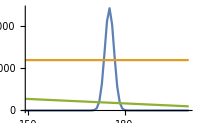

```mathematica
αα2[[1]]
```

```mathematica
?αα2
```

```mathematica
Plot[{f2[uρ,β2⟦1;;All,1⟧[[2]]],1/2 f2[β2⟦1;;All,1⟧[[1]],β2⟦1;;All,1⟧[[1]]],blin[β2⟦1;;All,1⟧[[1]],uρ]},{uρ,-16+Roi[β2⟦1;;All,1⟧[[1]]]⟦1⟧,16+Roi[β2⟦1;;All,1⟧[[1]]]⟦2⟧},PlotPoints->2,ImageSize->200,PlotRange->{Automatic,All}]
```

-Graphics-

```mathematica
fw[[1]]
```

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

```mathematica
CreateDialog[{DynamicModule[{c=1,min=1,max=Length[β2⟦1;;All,1⟧],a1=αα1,a2=αα2,a3=αα3,fff="",nm,ns,qq,xyx={"..."},xxx,xax,xzx},TabView[{"Show"->Dynamic[Grid[{{Column[{Row[{CancelButton[],Button["PrintPDF",FrontEndTokenExecute["PrintDialog"]],Button["Find",Dynamic[If[1≤nm≤max||NumberQ[nm],c=nm,CreateDialog[{TextCell["Not-Found"],ChoiceButtons[]}]]]],InputField[Dynamic[nm],Number,FieldHint->"N.Peak",ImageSize->{60,20}],"n",InputField[Dynamic[nm],Number,FieldHint->"chnall",ImageSize->{60,20}],"ch",InputField[Dynamic[nm],Number,FieldHint->"Energy (kev)",ImageSize->{60,20}],"Energy",Button["Find",Dynamic[If[MemberQ[H,ns,2],c=First[Position[H,ToString[ns]]⟦1⟧],CreateDialog[{TextCell["Not-Found"],ChoiceButtons[]}]]]],InputField[Dynamic[ns],String,FieldHint->"Name Elmaint",ImageSize->{60,20}],"Name",FileNameSetter[Dynamic[fff]],InputField[Text[Dynamic[fff]],Enabled->False,Appearance->"Framed"]}],Button["Prevus",c--,Enabled->Dynamic[c>min],Alignment->Center],{Dynamic[c],"channl="<>ToString[β2⟦1;;All,1⟧⟦c⟧],"Energy="<>ToString[fchanll[β2⟦1;;All,1⟧⟦c⟧]],"Fwhm="<>ToString[fw⟦c⟧],"NPA="<>ToString[NPA[β2⟦1;;All,1⟧⟦c⟧]]},Button["+",c++,Enabled->Dynamic[c<max]],a1⟦c⟧,tab11⟦c⟧}],Column[{name[c],a2⟦c⟧,a3⟦c⟧,tabspect⟦c⟧}]}}]],"Spectrum"->b,"Decy Elemnt"->ccc,"Generetor"->Row[{Button["Add",xyx=Append[xyx,RandomReal[]]],Dynamic[ListPicker[Dynamic[xax],xyx,ImageSize->450,FieldSize->{60,25},BaseStyle->{"DisplayFormulaNumbered"}]],Column[{Button["LodeCNF",qq=Flatten[{SystemDialogInput["FileOpen",".CNF"]}];xyx=Join[xyx,qq],Method->"Queued"],Button["Analysis",Dynamic[xxx=xax],ImageSize->50],InputField[Style[Text[Dynamic[xxx]],25,Red],Enabled->False,Appearance->"Framed",ImageSize->{350,35}]}],{ColorSetter[Dynamic[xa]]}}]}],DynamicUpdating->False],Row[{CancelButton[],Button["PrintPDF",FrontEndTokenExecute["PrintDialog"]],FileNameSetter[Dynamic[fff]],InputField[Text[Dynamic[fff]],Enabled->False,Appearance->"Framed"]}]},Enabled->True,WindowSize->{940,500},Background->Lighter[Orange,0.97],WindowElements->"VerticalScrollBar"]
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

q6f94_shm74FrontEndObject[LinkObject["q6f94_shm", 3, 1]]7474

```mathematica
(-12+roi[[1]]);;(12+roi[[2]])
```

```mathematica
β2β2kg[[3]]
```

175

```mathematica
CreateDialog[
Manipulate[
Module[{ppol,roi,plots,llst=sll,CC=β2β2kg[[c]]},

(*If[!Cch,llst=ReplaceAll[llst,{{αβ_,αg_}->{fchanll[αβ],αg}}]];*)

(*If[!Cch,CC=ReplaceAll[CC,{αβ_->fchanll[αβ]}]];*)


ppol=ReplaceAll[ pol[CC],

{If[!Cch,{αβ_,αg_}->{fchanll[αβ],αg},{αβ_,αg_}->{fchtoene[fchanll[αβ]],αg}]

}];

If[plottyp==ListLogPlot,ppol=ReplaceAll[ppol,{αβ_,αg_/;αg!=0}->{αβ,Log[αg]}]];
If[plottyp==ListLogLogPlot,ppol=ReplaceAll[ppol,{αβ_/;αβ!=0->Log[αβ]}]];
If[plottyp==ListLogLinearPlot,ppol=ReplaceAll[ppol,{αβ_/;αβ!=0,αg_}->{Log[αβ],αg}]];


ep=Which[poly==0,{},poly==1,

{Brown,Opacity[0.3],ppol,Block[{x=xxbkg,β2=β2kg,Bppol},Bppol=ReplaceAll[ pol[CC],If[!Cch,{αβ_,αg_}->{fchanll[αβ],αg},{αβ_,αg_}->{fchtoene[fchanll[αβ]],αg}]];
If[plottyp==ListLogPlot,Bppol=ReplaceAll[Bppol,{αβ_,αg_/;αg!=0}->{αβ,Log[αg]}]];
If[plottyp==ListLogLogPlot,Bppol=ReplaceAll[Bppol,{αβ_/;αβ!=0->Log[αβ]}]];If[plottyp==ListLogLinearPlot,Bppol=ReplaceAll[Bppol,{αβ_/;αβ!=0,αg_}->{Log[αβ],αg}]];Bppol ]},

poly==2,{Brown,Opacity[0.3],ppol},

poly==3,{Brown,Opacity[0.3],Block[{x=xxbkg,β2=β2kg,Bppol},Bppol=ReplaceAll[ pol[CC],If[!Cch,{αβ_,αg_}->{fchanll[αβ],αg},{αβ_,αg_}->{fchtoene[fchanll[αβ]],αg}]];
If[plottyp==ListLogPlot,Bppol=ReplaceAll[Bppol,{αβ_,αg_/;αg!=0}->{αβ,Log[αg]}]];
If[plottyp==ListLogLogPlot,Bppol=ReplaceAll[Bppol,{αβ_/;αβ!=0,αg_/;αg!=0}->{Log[αβ],Log[αg]}]];If[plottyp==ListLogLinearPlot,Bppol=ReplaceAll[Bppol,{αβ_/;αβ!=0,αg_}->{Log[αβ],αg}]];Bppol ]}];



Which[llst==lst0,roi=Block[{x=First@lst0},Roi[CC]],llst==lst1,roi=Block[{x=First@lst1},Roi[CC]],llst==lst00,roi=MinMax[Flatten[{Block[{x=First@lst1},Roi[CC]],Block[{x=First@lst0},Roi[CC]]}]]];


plots={plottyp[Map[ReplaceAll[(#[[(-12+roi[[1]]);;(12+roi[[2]])]]),]&,llst],PlotRange->Full,

ImageSize->700,AspectRatio->1/2,GridLines->Full,Filling->Filing,Joined->jnd,Mesh->Full,

MeshStyle->{{Red, PointSize[0.01]},{Pink, PointSize[0.01]}},Ticks->{(*Range@@({-16,16}+Roi[175])*)All, Automatic},

InterpolationOrder->inp,PlotTheme->plothem,Epilog->Union[{ep,Black,PointSize[0.03]},Map[Point,(Flatten[Nearest[First@Map[ReplaceAll[(#[[(-12+Roi[β2[[;;,1]][[c]]][[1]]);;(12+Roi[β2[[;;,1]][[c]]][[2]])]]),If[!False,{αβ_,αg_}->{fchanll[αβ],αg},{αβ_,αg_}->{fchtoene[fchanll[αβ]],αg}]]&,lst0],mark],1])] ]]};


(*If[(llst!=lst00 )&&TrueQ[Filing==={1->{2}}],];*)


Show[plots]

],Delimiter,
Dynamic@Pane[If[MemberQ[β2[[;;,1]],β2β2kg[[c]]],Style[TableForm[{data00[[c]]},TableHeadings->{None, {"Energy","G[e]&&T[e]","Neclud","Star Beak","Activty","Chanll","FWHM","ROI","NPA","A.poly","A.Between","HalfLife"}}],{Medium,Bold,Black}],Style[TableForm[{data00[[c]]},TableHeadings->{None, {"Energy","G[e]&&T[e]","Neclud","Star Beak","Activty","Chanll","FWHM","ROI","NPA","A.poly","A.Between","HalfLife"}}],{Medium,Bold,LightGray}]],ImageSize->900,ImageSizeAction->"ResizeToFit",AppearanceElements->None]

,Delimiter,

Dynamic@
Pane[If[MemberQ[β2kg[[;;,1]],β2β2kg[[c]]],Style[TableForm[{data00[[c]]},TableHeadings->{None, {"Energy","G[e]&&T[e]","Neclud","Star Beak","Activty","Chanll","FWHM","ROI","NPA","A.poly","A.Between","HalfLife"}}],{Medium,Bold,Black}],Style[TableForm[{data00[[c]]},TableHeadings->{None, {"Energy","G[e]&&T[e]","Neclud","Star Beak","Activty","Chanll","FWHM","ROI","NPA","A.poly","A.Between","HalfLife"}}],{Medium,Bold,LightGray}]],ImageSize->900,ImageSizeAction->"ResizeToFit",AppearanceElements->None]

,Dynamic[Canvas[Row[{name[c],Block[,name[c]]}]]],
Delimiter

,Button["Show more Information",CreatePalette[Grid[{{Dynamic[Canvas[name[c]]],Dynamic[Canvas[αα2[[c]]]],Dynamic[Canvas[αα3[[c]]]]}}]]]


,Delimiter,Control[{{sll,lst00,""},{lst00->"All",lst0->"ShowSpectrum",lst1->"ShowBKG"},ControlType->RadioButtonBar}],
Control[{{plothem,None,""},{None->"Normal","Scientific"->"Scientific","BlackBackground"->"BBG"},ControlType->RadioButtonBar}],
Control[{{inp,1,""},{0->"Discrite",1->"Normal",2->"Smooth"},ControlType->RadioButtonBar}],
Delimiter,
Dynamic@Column[{Control@{{c,1,Dynamic@β2β2kg[[c]]},Button["random",If[c>=max,c=max,c++],ImageSize->170]&},Control[{c,1,max,1,ControlType->Slider,Appearance->{"DownArrow",Large},ImageSize->170}],Control@{{c,1,Dynamic@β2β2kg[[c]]},Button["random",If[c<=1,c=1,c--],ImageSize->170]&}}],
Delimiter,

Pane[Column[{
Row[{Style["Joind",Bold,Medium],
Control[{{jnd,True,""},{True->"ShowBKG",False->"ShowPGN"},ControlType->Checkbox}],Style["AxisType",Bold,Medium],
Control[{{Cch,True,""},{True->"Chnall",False->"Energy"},ControlType->RadioButtonBar}]}],

Control[{{fit,1,""},{1->"Nofit",2->"fit",3->"fitAll"},ControlType->RadioButtonBar}],
Control[{{ShowCrev,1,""},{1->"None",2->"ShowCrev"},ControlType->RadioButtonBar}]}]],


Delimiter,


Delimiter(*,Style["Opstion",Bold,Medium]*),

Row[{Pane[Column[{
Style["Filling",Bold,Medium],
Control[{{Filing,Axis,""},{None->"None",Axis->"ShowBKG",Top->"ShowPGN",{2->{{1},{HatchFilling[π/4,3,3],HatchFilling[π/6,2,2]}}}->"Between"},ControlType->RadioButtonBar,Appearance -> "Vertical" -> {Automatic,1}}]}]],
Pane[Column[{
Style["plottyp",Bold,Medium],
Control[{{plottyp,ListPlot,""},{ListPlot->"Normal",ListLogPlot->"LLP",ListLogLogPlot->"LLLP",ListLogLinearPlot->"Log.X"},ControlType->RadioButtonBar,Appearance -> "Vertical" -> {Automatic,1}}]}]]
,"     ",
Pane[Column[{Style["polyShow",Bold,Medium],Control[{{poly,0,""},{0->"None",1->"All",2->"ShowSpoly",3->"ShowBpoly"},ControlType->RadioButtonBar,Appearance -> "Vertical" -> {Automatic,1}}]}]]
}]
,
{{mark,Dynamic[lst0[[1,#]]&/@Roi[β2[[;;,1]][[c]]]]},Locator,Appearance->None}








,
ControlPlacement->Flatten@{Bottom,Bottom,Table[Right,9]},AppearanceElements->None,Initialization:>{lst0=,lst1=,lst00=First/@{lst0,lst1},β2β2kg=Union@@{β2[[;;,1]],β2kg[[;;,1]]},max=Length[β2β2kg],dat1=Thread[{H⟦1;;All,1⟧,ToString/@A/@H⟦1;;All,1⟧,ToString/@(B/.{}->"--"),ToString/@bbb,ToString/@Activc1,ToString/@β2⟦1;;All,1⟧,ToString/@fw,ToString/@Roi/@β2⟦1;;All,1⟧,ToString/@q⟦1;;All,2⟧,ToString/@(N@Area[pol[#]]&/@β2⟦1;;All,1⟧),ToString/@(Total[x⟦Roi[#1]⟦1⟧;;Roi[#1]⟦2⟧,2⟧-xxbkg⟦Roi[#1]⟦1⟧;;Roi[#1]⟦2⟧,2⟧]&/@β2⟦1;;All,1⟧),Map[ToString[#,TraditionalForm]&,Map[If[#=="--","--",IsotopeData[#,"HalfLife"]]&,hl,{2}]]}],


dat2=Block[{x=xxbkg,H=Hkg,hl=hlkg,B=Bkg,bbb=bbbkg,β2=β2kg,fw=fwkg,q=qkg},Thread[{H⟦1;;All,1⟧,ToString/@A/@H⟦1;;All,1⟧,ToString/@(B/.{}->"--"),ToString/@bbb,ToString/@Activc1,ToString/@β2⟦1;;All,1⟧,ToString/@fw,ToString/@Roi/@β2⟦1;;All,1⟧,ToString/@q⟦1;;All,2⟧,ToString/@(N@Area[pol[#]]&/@β2⟦1;;All,1⟧),ToString/@(Total[x⟦Roi[#1]⟦1⟧;;Roi[#1]⟦2⟧,2⟧-xxbkg⟦Roi[#1]⟦1⟧;;Roi[#1]⟦2⟧,2⟧]&/@β2⟦1;;All,1⟧),Map[ToString[#,TraditionalForm]&,Map[If[#=="--","--",IsotopeData[#,"HalfLife"]]&,hl,{2}]]}]],data00=Sort@Join[dat1,dat2]}],Deployed->True,Selectable->False,WindowSize->All,WindowElements->{"VerticalScrollBar"}]
```

swgcd_shm79FrontEndObject[LinkObject["swgcd_shm", 3, 1]]7979

```mathematica
c=.
```

```mathematica
Map[Point,(Flatten[Nearest[First@Map[ReplaceAll[(#[[(-12+Roi[β2[[;;,1]][[c]]][[1]]);;(12+Roi[β2[[;;,1]][[c]]][[2]])]]),If[!False,{αβ_,αg_}->{fchanll[αβ],αg},{αβ_,αg_}->{fchtoene[fchanll[αβ]],αg}]]&,lst0],lst0[[1,#]]&/@Roi[β2[[;;,1]][[c]]]],1])]
```

```mathematica
Map[Point,(Flatten[Nearest[First@Map[ReplaceAll[(#[[(-12+roi[[1]]);;(12+roi[[2]])]]),]&,llst],mark],1])]
```

```mathematica
c=.
```

```mathematica
β2β2kg[[3]]
```

175

```mathematica
MapThread[]
```

```mathematica
Roi[175]
```

{165,184}

```mathematica
β2[[;;,1]][[1]]
```

175

```mathematica
Roi[β2[[;;,1]][[1]]]
```

{165,184}

```mathematica
lst0[[1,#]]&/@Roi[β2[[;;,1]][[1]]]
```

{{165,439},{184,307}}

```mathematica
Roi[175]
```

{165,184}

```mathematica
lst0[[1,Roi[175][[1]];;Roi[175][[2]]]]
```

{{165,439},{166,473},{167,505},{168,513},{169,523},{170,522},{171,554},{172,753},{173,1349},{174,3088},{175,4843},{176,4358},{177,2066},{178,714},{179,411},{180,332},{181,346},{182,320},{183,320},{184,307}}

```mathematica
Flatten[Nearest[lst0[[1,Roi[175][[1]];;Roi[175][[2]]]],lst0[[1,#]]&/@Roi[175]],1]
```

{{165,439},{184,307}}

```mathematica
Thread[{H⟦1;;All,1⟧,ToString/@A/@H⟦1;;All,1⟧,ToString/@(B/.{}->"--"),ToString/@bbb,ToString/@Activc1,ToString/@β2⟦1;;All,1⟧,ToString/@fw,ToString/@Roi/@β2⟦1;;All,1⟧,ToString/@q⟦1;;All,2⟧,ToString/@(N@Area[pol[#]]&/@β2⟦1;;All,1⟧),ToString/@(Total[x⟦Roi[#1]⟦1⟧;;Roi[#1]⟦2⟧,2⟧-xxbkg⟦Roi[#1]⟦1⟧;;Roi[#1]⟦2⟧,2⟧]&/@β2⟦1;;All,1⟧)}]
```

```mathematica
{{59.63868027463983,"True","{Am-241}","{True}","213.969","175","3.40456","{165, 184}","15276.","7087.","14715"},{74.96747570257531,"False","--","--","--","220","14.7546","{210, 224}","2018.","6468.","-111"},{77.35195499136528,"False","--","--","--","227","4.48198","{224, 231}","3357.","3157.","3350"},{84.50539285773517,"False","--","--","--","248","14.4533","{244, 252}","401.5","2804.","-1651"},{87.57115194332226,"True","{Cd-109}","{False}","5.13027","257","7.5121","{252, 261}","1844.","3132.","534"},{89.95563123211222,"False","--","--","--","264","10.1973","{261, 269}","678.","2504.","-190"},{186.35672247890648,"True","{U-235, Ra-226}","{True, False}","6.58721","547","8.69627","{538, 553}","3433.","4800.","465"},{204.41063709403048,"True","{U-235}","{True}","0.591549","600","Erorr","{593, 607}","291.5","2524.5","-1763"},{223.82711130274876,"False","--","--","--","657","8.51947","{654, 658}","126.","988.","-539"},{241.88102591787276,"True","{Pb-214}","{True}","12.402","710","4.63476","{705, 718}","5430.","3087.5","3324"},{259.25366073619966,"True","{Pa-234m}","{False}","1.86203","761","27.7794","{753, 771}","768.","3474.","-2020"},{274.9230960625337,"True","{Cs-136, Ba-133}","{False, False}","0.394481","807","48.7486","{797, 809}","156.5","2490.","-1342"},{295.36148996644766,"True","{Pb-214, Au-194, Xe-139}","{True, False, True}","32.2203","867","Erorr","{859, 877}","12083.","3024.","9029"},{351.90771310060967,"True","{Pb-214}","{True}","61.8326","1033","Erorr","{1023, 1040}","20294.","2575.5","17559"},{389.3781019244519,"False","--","--","--","1143","Erorr","{1137, 1152}","177.","1770.","-1320"},{469.08783814971645,"False","--","--","--","1377","Erorr","{1368, 1382}","224.","1148.","-1133"},{480.32895479686914,"False","--","--","--","1410","8.77298","{1406, 1413}","182.","514.5","-543"},{487.1417527648405,"False","--","--","--","1430","22.6688","{1420, 1433}","234.","923.","-1136"},{533.809418845444,"False","--","--","--","1567","16.0919","{1561, 1573}","257.5","546.","-1159"},{580.1364450276491,"False","--","--","--","1703","21.8354","{1693, 1709}","61.5","856.","-1537"},{609.0908363915272,"True","{Bi-214}","{True}","71.6779","1788","4.31585","{1778, 1798}","15844.5","1090.","13097"},{622.3757924290712,"False","--","--","--","1827","Erorr","{1820, 1828}","53.5","268.","-873"},{661.2087408465078,"True","{Cs-137}","{True}","50.595","1941","Erorr","{1931, 1947}","10502.5","600.","9002"},{664.955779728892,"False","--","--","--","1952","7.14635","{1947, 1960}","466.","403.","-803"},{690.5037721087845,"False","--","--","--","2027","Erorr","{2026, 2028}","16.5","49.","-261"},{719.4581634726626,"False","--","--","--","2112","15.1732","{2103, 2120}","238.","314.5","-1500"},{768.1696689436576,"True","{Zn-65, Pa-234m}","{False, False}","8.10734","2255","5.51186","{2245, 2264}","1513.","437.","-345"},{785.5423037619845,"True","{Pb-214, Pa-234m}","{True, False}","2.42456","2306","9.0541","{2299, 2316}","441.","306.","-1121"},{795.0802209171443,"True","{Cs-134}","{True}","0.501527","2334","12.594","{2328, 2339}","91.","176.","-1007"},{805.6400577674999,"True","{Ag-99}","{False}","2.54244","2365","10.2983","{2357, 2375}","459.5","333.","-1258"},{838.6821279121608,"False","--","--","--","2462","11.7554","{2453, 2470}","237.","357.","-1277"},{893.8657914527286,"False","--","--","--","2624","20.7396","{2617, 2631}","41.","322.","-996"},{933.7206595653607,"False","--","--","--","2741","6.11852","{2731, 2747}","791.5","344.","-391"},{1120.0506839893765,"True","{Bi-214}","{True}","24.9387","3288","5.52403","{3278, 3296}","3495.5","351.","2044"},{1132.995000128522,"False","--","--","--","3326","12.9242","{3319, 3332}","79","182.","-748"},{1155.1365935244287,"False","--","--","--","3391","8.41531","{3383, 3401}","445.","216.","-729"},{1237.5714489368818,"True","{Bi-214, Cs-136}","{True, False}","9.47725","3633","6.24278","{3627, 3643}","1231.5","264.","162"},{1280.4920761351011,"False","--","--","--","3759","8.57629","{3750, 3769}","403.","152.","-584"},{1377.2338072802938,"False","--","--","--","4043","6.26235","{4033, 4053}","962.5","170.","-16"},{1385.068524943461,"True","{Y-88}","{False}","1.89004","4066","10.2993","{4056, 4072}","226.5","120.","-411"},{1401.419240066592,"False","--","--","--","4114","8.39314","{4104, 4124}","210.","142.5","-460"},{1407.891398136165,"False","--","--","--","4133","7.55101","{4123, 4143}","552.5","110.","-342"},{1509.061447960539,"False","--","--","--","4430","8.14247","{4423, 4440}","404.","187.","-113"},{1583.3209458114266,"False","--","--","--","4648","8.32475","{4641, 4657}","190.5","72.","-217"},{1660.9868426462995,"False","--","--","--","4876","7.94111","{4867, 4883}","225","32.","-173"},{1729.4554622244113,"False","--","--","--","5077","6.54162","{5067, 5087}","626","60.","67"},{1764.5413717594638,"True","{Bi-214}","{True}","25.8327","5180","6.17045","{5170, 5190}","2687.5","130.","1394"},{1847.657506968714,"True","{Bi-203}","{False}","3.16738","5424","6.21983","{5414, 5434}","323.5","28.5","-135"},{2204.98876038881,"True","{Bi-214}","{True}","6.79715","6473","7.72435","{6463, 6482}","674.","47.5","16"},{2448.2056478453865,"False","--","--","--","7187","7.17989","{7177, 7197}","235","Undefined","-113"}}
```

{{59.6387,True,{Am-241},{True},213.969,175,3.40456,{165, 184},15276.,7087.,14715},{74.9675,False,--,--,--,220,14.7546,{210, 224},2018.,6468.,-111},{77.352,False,--,--,--,227,4.48198,{224, 231},3357.,3157.,3350},{84.5054,False,--,--,--,248,14.4533,{244, 252},401.5,2804.,-1651},{87.5712,True,{Cd-109},{False},5.13027,257,7.5121,{252, 261},1844.,3132.,534},{89.9556,False,--,--,--,264,10.1973,{261, 269},678.,2504.,-190},{186.357,True,{U-235, Ra-226},{True, False},6.58721,547,8.69627,{538, 553},3433.,4800.,465},{204.411,True,{U-235},{True},0.591549,600,Erorr,{593, 607},291.5,2524.5,-1763},{223.827,False,--,--,--,657,8.51947,{654, 658},126.,988.,-539},{241.881,True,{Pb-214},{True},12.402,710,4.63476,{705, 718},5430.,3087.5,3324},{259.254,True,{Pa-234m},{False},1.86203,761,27.7794,{753, 771},768.,3474.,-2020},{274.923,True,{Cs-136, Ba-133},{False, False},0.394481,807,48.7486,{797, 809},156.5,2490.,-1342},{295.361,True,{Pb-214, Au-194, Xe-139},{True, False, True},32.2203,867,Erorr,{859, 877},12083.,3024.,9029},{351.908,True,{Pb-214},{True},61.8326,1033,Erorr,{1023, 1040},20294.,2575.5,17559},{389.378,False,--,--,--,1143,Erorr,{1137, 1152},177.,1770.,-1320},{469.088,False,--,--,--,1377,Erorr,{1368, 1382},224.,1148.,-1133},{480.329,False,--,--,--,1410,8.77298,{1406, 1413},182.,514.5,-543},{487.142,False,--,--,--,1430,22.6688,{1420, 1433},234.,923.,-1136},{533.809,False,--,--,--,1567,16.0919,{1561, 1573},257.5,546.,-1159},{580.136,False,--,--,--,1703,21.8354,{1693, 1709},61.5,856.,-1537},{609.091,True,{Bi-214},{True},71.6779,1788,4.31585,{1778, 1798},15844.5,1090.,13097},{622.376,False,--,--,--,1827,Erorr,{1820, 1828},53.5,268.,-873},{661.209,True,{Cs-137},{True},50.595,1941,Erorr,{1931, 1947},10502.5,600.,9002},{664.956,False,--,--,--,1952,7.14635,{1947, 1960},466.,403.,-803},{690.504,False,--,--,--,2027,Erorr,{2026, 2028},16.5,49.,-261},{719.458,False,--,--,--,2112,15.1732,{2103, 2120},238.,314.5,-1500},{768.17,True,{Zn-65, Pa-234m},{False, False},8.10734,2255,5.51186,{2245, 2264},1513.,437.,-345},{785.542,True,{Pb-214, Pa-234m},{True, False},2.42456,2306,9.0541,{2299, 2316},441.,306.,-1121},{795.08,True,{Cs-134},{True},0.501527,2334,12.594,{2328, 2339},91.,176.,-1007},{805.64,True,{Ag-99},{False},2.54244,2365,10.2983,{2357, 2375},459.5,333.,-1258},{838.682,False,--,--,--,2462,11.7554,{2453, 2470},237.,357.,-1277},{893.866,False,--,--,--,2624,20.7396,{2617, 2631},41.,322.,-996},{933.721,False,--,--,--,2741,6.11852,{2731, 2747},791.5,344.,-391},{1120.05,True,{Bi-214},{True},24.9387,3288,5.52403,{3278, 3296},3495.5,351.,2044},{1133.,False,--,--,--,3326,12.9242,{3319, 3332},79,182.,-748},{1155.14,False,--,--,--,3391,8.41531,{3383, 3401},445.,216.,-729},{1237.57,True,{Bi-214, Cs-136},{True, False},9.47725,3633,6.24278,{3627, 3643},1231.5,264.,162},{1280.49,False,--,--,--,3759,8.57629,{3750, 3769},403.,152.,-584},{1377.23,False,--,--,--,4043,6.26235,{4033, 4053},962.5,170.,-16},{1385.07,True,{Y-88},{False},1.89004,4066,10.2993,{4056, 4072},226.5,120.,-411},{1401.42,False,--,--,--,4114,8.39314,{4104, 4124},210.,142.5,-460},{1407.89,False,--,--,--,4133,7.55101,{4123, 4143},552.5,110.,-342},{1509.06,False,--,--,--,4430,8.14247,{4423, 4440},404.,187.,-113},{1583.32,False,--,--,--,4648,8.32475,{4641, 4657},190.5,72.,-217},{1660.99,False,--,--,--,4876,7.94111,{4867, 4883},225,32.,-173},{1729.46,False,--,--,--,5077,6.54162,{5067, 5087},626,60.,67},{1764.54,True,{Bi-214},{True},25.8327,5180,6.17045,{5170, 5190},2687.5,130.,1394},{1847.66,True,{Bi-203},{False},3.16738,5424,6.21983,{5414, 5434},323.5,28.5,-135},{2204.99,True,{Bi-214},{True},6.79715,6473,7.72435,{6463, 6482},674.,47.5,16},{2448.21,False,--,--,--,7187,7.17989,{7177, 7197},235,Undefined,-113}}

```mathematica
Thread[{H⟦1;;All,1⟧,ToString/@A/@H⟦1;;All,1⟧,ToString/@(B/.{}->"--"),ToString/@bbb,ToString/@Activc1,ToString/@β2⟦1;;All,1⟧,ToString/@fw,ToString/@Roi/@β2⟦1;;All,1⟧,ToString/@q⟦1;;All,2⟧,ToString/@(N@Area[pol[#]]&/@β2⟦1;;All,1⟧),ToString/@(Total[x⟦Roi[#1]⟦1⟧;;Roi[#1]⟦2⟧,2⟧-xxbkg⟦Roi[#1]⟦1⟧;;Roi[#1]⟦2⟧,2⟧]&/@β2⟦1;;All,1⟧),Map[ToString[#,TraditionalForm]&,Map[If[#=="--","--",IsotopeData[#,"HalfLife"]]&,hl,{2}]]}]
```

```mathematica
MemberQ[β2[[;;,1]],β2β2kg[[3]]]
```

True

```mathematica
data00[[2]]
```

{53.5072,True,{Ce-144, Pb-214},{False, True},17.9627,157,Erorr,{149, 165},574.5,4260.}

```mathematica
Sort@Join[dat1,dat2]
```

```mathematica
{{59.63868027463983,"True","{Am-241}","{True}","213.969","175","3.40456","{165, 184}","15276.","7087.","14715"},{74.96747570257531,"False","--","--","--","220","14.7546","{210, 224}","2018.","6468.","-111"},{77.35195499136528,"False","--","--","--","227","4.48198","{224, 231}","3357.","3157.","3350"},{84.50539285773517,"False","--","--","--","248","14.4533","{244, 252}","401.5","2804.","-1651"},{87.57115194332226,"True","{Cd-109}","{False}","5.13027","257","7.5121","{252, 261}","1844.","3132.","534"},{89.95563123211222,"False","--","--","--","264","10.1973","{261, 269}","678.","2504.","-190"},{186.35672247890648,"True","{U-235, Ra-226}","{True, False}","6.58721","547","8.69627","{538, 553}","3433.","4800.","465"},{204.41063709403048,"True","{U-235}","{True}","0.591549","600","Erorr","{593, 607}","291.5","2524.5","-1763"},{223.82711130274876,"False","--","--","--","657","8.51947","{654, 658}","126.","988.","-539"},{241.88102591787276,"True","{Pb-214}","{True}","12.402","710","4.63476","{705, 718}","5430.","3087.5","3324"},{259.25366073619966,"True","{Pa-234m}","{False}","1.86203","761","27.7794","{753, 771}","768.","3474.","-2020"},{274.9230960625337,"True","{Cs-136, Ba-133}","{False, False}","0.394481","807","48.7486","{797, 809}","156.5","2490.","-1342"},{295.36148996644766,"True","{Pb-214, Au-194, Xe-139}","{True, False, True}","32.2203","867","Erorr","{859, 877}","12083.","3024.","9029"},{351.90771310060967,"True","{Pb-214}","{True}","61.8326","1033","Erorr","{1023, 1040}","20294.","2575.5","17559"},{389.3781019244519,"False","--","--","--","1143","Erorr","{1137, 1152}","177.","1770.","-1320"},{469.08783814971645,"False","--","--","--","1377","Erorr","{1368, 1382}","224.","1148.","-1133"},{480.32895479686914,"False","--","--","--","1410","8.77298","{1406, 1413}","182.","514.5","-543"},{487.1417527648405,"False","--","--","--","1430","22.6688","{1420, 1433}","234.","923.","-1136"},{533.809418845444,"False","--","--","--","1567","16.0919","{1561, 1573}","257.5","546.","-1159"},{580.1364450276491,"False","--","--","--","1703","21.8354","{1693, 1709}","61.5","856.","-1537"},{609.0908363915272,"True","{Bi-214}","{True}","71.6779","1788","4.31585","{1778, 1798}","15844.5","1090.","13097"},{622.3757924290712,"False","--","--","--","1827","Erorr","{1820, 1828}","53.5","268.","-873"},{661.2087408465078,"True","{Cs-137}","{True}","50.595","1941","Erorr","{1931, 1947}","10502.5","600.","9002"},{664.955779728892,"False","--","--","--","1952","7.14635","{1947, 1960}","466.","403.","-803"},{690.5037721087845,"False","--","--","--","2027","Erorr","{2026, 2028}","16.5","49.","-261"},{719.4581634726626,"False","--","--","--","2112","15.1732","{2103, 2120}","238.","314.5","-1500"},{768.1696689436576,"True","{Zn-65, Pa-234m}","{False, False}","8.10734","2255","5.51186","{2245, 2264}","1513.","437.","-345"},{785.5423037619845,"True","{Pb-214, Pa-234m}","{True, False}","2.42456","2306","9.0541","{2299, 2316}","441.","306.","-1121"},{795.0802209171443,"True","{Cs-134}","{True}","0.501527","2334","12.594","{2328, 2339}","91.","176.","-1007"},{805.6400577674999,"True","{Ag-99}","{False}","2.54244","2365","10.2983","{2357, 2375}","459.5","333.","-1258"},{838.6821279121608,"False","--","--","--","2462","11.7554","{2453, 2470}","237.","357.","-1277"},{893.8657914527286,"False","--","--","--","2624","20.7396","{2617, 2631}","41.","322.","-996"},{933.7206595653607,"False","--","--","--","2741","6.11852","{2731, 2747}","791.5","344.","-391"},{1120.0506839893765,"True","{Bi-214}","{True}","24.9387","3288","5.52403","{3278, 3296}","3495.5","351.","2044"},{1132.995000128522,"False","--","--","--","3326","12.9242","{3319, 3332}","79","182.","-748"},{1155.1365935244287,"False","--","--","--","3391","8.41531","{3383, 3401}","445.","216.","-729"},{1237.5714489368818,"True","{Bi-214, Cs-136}","{True, False}","9.47725","3633","6.24278","{3627, 3643}","1231.5","264.","162"},{1280.4920761351011,"False","--","--","--","3759","8.57629","{3750, 3769}","403.","152.","-584"},{1377.2338072802938,"False","--","--","--","4043","6.26235","{4033, 4053}","962.5","170.","-16"},{1385.068524943461,"True","{Y-88}","{False}","1.89004","4066","10.2993","{4056, 4072}","226.5","120.","-411"},{1401.419240066592,"False","--","--","--","4114","8.39314","{4104, 4124}","210.","142.5","-460"},{1407.891398136165,"False","--","--","--","4133","7.55101","{4123, 4143}","552.5","110.","-342"},{1509.061447960539,"False","--","--","--","4430","8.14247","{4423, 4440}","404.","187.","-113"},{1583.3209458114266,"False","--","--","--","4648","8.32475","{4641, 4657}","190.5","72.","-217"},{1660.9868426462995,"False","--","--","--","4876","7.94111","{4867, 4883}","225","32.","-173"},{1729.4554622244113,"False","--","--","--","5077","6.54162","{5067, 5087}","626","60.","67"},{1764.5413717594638,"True","{Bi-214}","{True}","25.8327","5180","6.17045","{5170, 5190}","2687.5","130.","1394"},{1847.657506968714,"True","{Bi-203}","{False}","3.16738","5424","6.21983","{5414, 5434}","323.5","28.5","-135"},{2204.98876038881,"True","{Bi-214}","{True}","6.79715","6473","7.72435","{6463, 6482}","674.","47.5","16"},{2448.2056478453865,"False","--","--","--","7187","7.17989","{7177, 7197}","235","Undefined","-113"},{47.03500403389288,"False","--","--","--","138","Erorr","{133, 147}","341.5","5411."},{53.507162103465646,"True","{Ce-144, Pb-214}","{False, True}","17.9627","157","Erorr","{149, 165}","574.5","4260."},{63.38571915702406,"True","{Th-232}","{False}","5.0036","186","Erorr","{176, 191}","514.","5767.5"},{66.79211814100972,"False","--","--","--","196","15.6384","{191, 198}","266.","2635.5"},{72.92363631218392,"True","{Hg-203}","{False}","3.31342","214","7.73878","{211, 217}","667.","2682."},{75.30811560097388,"False","--","--","--","221","6.28853","{217, 224}","1696.","3150."},{84.84603275613374,"False","--","--","--","249","13.369","{242, 254}","1371.","5160."},{87.57115194332226,"True","{Cd-109}","{False}","1.43559","257","10.4782","{254, 261}","516.","2863."},{92.68075041930076,"False","--","--","--","272","19.6288","{262, 280}","2094.","6786."},{140.02969629670147,"True","{Th-232, Tc-99m}","{False, False}","0.718053","411","20.1659","{408, 416}","407.5","3524."},{143.7767351790857,"True","{Fe-59, U-235, Tc-99m}","{False, True, False}","1.05946","422","21.7929","{416, 427}","600.","4856.5"},{186.0160825805079,"True","{U-235, Ra-226}","{True, False}","3.07595","546","17.4627","{537, 552}","1605.","6045."},{196.57591943086345,"True","{At-209}","{False}","0.239982","577","Erorr","{571, 582}","121.","4620."},{205.43255678922617,"True","{U-235}","{True}","0.838858","603","Erorr","{599, 611}","412.","2964."},{238.8152668322857,"True","{Pb-212, At-209}","{False, False}","2.0439","701","16.2106","{693, 706}","904.","4959.5"},{295.0208500680491,"True","{Pb-214, Au-194, Xe-139}","{True, False, True}","2.02753","866","18.6217","{861, 874}","761.","3718."},{338.282117164667,"True","{Ac-228}","{False}","1.49588","993","19.0703","{987, 999}","507.","2832."},{351.90771310060967,"True","{Pb-214}","{True}","4.30824","1033","14.9458","{1023, 1038}","1414.","3315."},{510.6459057543415,"True","{Cs-142, Tl-208}","{False, False}","22.7323","1499","10.3541","{1489, 1509}","5700.","3700."},{582.8615642148376,"True","{Tl-208}","{False}","2.52432","1711","13.2288","{1706, 1718}","575.5","1578."},{609.0908363915272,"True","{Bi-214}","{True}","7.46433","1788","12.2219","{1779, 1796}","1650.","1759.5"},{633.2762691778254,"False","--","--","--","1859","Erorr","{1855, 1868}","157.","1540.5"},{638.3858676538039,"True","{I-131}","{False}","0.0113946","1874","Erorr","{1868, 1882}","2.5","1799."},{726.952241237431,"False","--","--","--","2134","Erorr","{2125, 2135}","99.","1140."},{802.2336587835142,"True","{Cs-134}","{True}","0.806206","2355","14.3126","{2350, 2359}","146.","913.5"},{910.2165065758597,"True","{Ac-228}","{False}","3.94854","2672","14.1893","{2667, 2682}","648.","1320."},{964.0376105228332,"True","{Ac-228}","{False}","1.14857","2830","Erorr","{2825, 2839}","180.5","1155."},{968.125289303616,"True","{Cs-142, Ac-228}","{False, False}","2.25528","2842","15.4235","{2839, 2852}","353.","1105."},{973.575527677993,"False","--","--","--","2858","8.56463","{2857, 2862}","82.","365."},{989.5856029027257,"False","--","--","--","2905","20.8764","{2904, 2910}","52.","268."},{1000.4860796514797,"True","{Pa-234m}","{False}","1.8196","2937","22.6267","{2928, 2942}","278","1008."},{1073.7236578071713,"False","--","--","--","3152","16.8187","{3146, 3153}","77.","465.5"},{1120.391323887775,"True","{Bi-214}","{True}","5.15952","3289","11.6038","{3281, 3295}","723.","742."},{1132.3137203317249,"False","--","--","--","3324","Erorr","{3319, 3327}","34.","568."},{1136.060759214109,"False","--","--","--","3335","Erorr","{3327, 3336}","56.","607.5"},{1157.8617127116172,"False","--","--","--","3399","12.3493","{3394, 3401}","107.","423.5"},{1377.5744471786925,"False","--","--","--","4044","13.7635","{4036, 4048}","237.5","486."},{1407.2101183393677,"False","--","--","--","4131","22.0775","{4122, 4141}","214.","703."},{1460.349942489544,"True","{K-40}","{False}","49.6412","4287","6.20799","{4277, 4297}","5741.","660."},{1509.061447960539,"False","--","--","--","4430","20.2519","{4425, 4439}","114.5","336."},{1587.7492644906079,"False","--","--","--","4661","15.4521","{4651, 4668}","72.","569.5"},{1615.3410962608916,"False","--","--","--","4742","Erorr","{4735, 4745}","47.5","205."},{1620.4506947368702,"False","--","--","--","4757","13.0932","{4748, 4763}","146.","330."},{1630.3292517904285,"False","--","--","--","4786","12.3785","{4782, 4794}","177.5","234."},{1730.1367420212084,"False","--","--","--","5079","16.3961","{5069, 5088}","268.","304."},{1734.56506070039,"False","--","--","--","5092","11.5372","{5088, 5096}","31.5","132."},{1764.2007318610652,"True","{Bi-214}","{True}","10.9479","5179","7.51505","{5169, 5187}","1139.","234."},{1804.0555999736973,"False","--","--","--","5296","5.44327","{5294, 5299}","34.","75."},{1847.3168670703153,"True","{Bi-203}","{False}","1.96792","5423","17.2602","{5413, 5433}","201.","320."},{1858.8986236158667,"False","--","--","--","5457","Erorr","{5455, 5464}","51.","130.5"},{1882.4027766053675,"False","--","--","--","5526","15.0579","{5518, 5531}","80","156."},{1910.3352482740502,"False","--","--","--","5608","19.7955","{5600, 5616}","91.5","232."},{2204.307480592013,"True","{Bi-214}","{True}","4.0755","6471","10.673","{6462, 6481}","404.","285."},{2615.1191980606836,"True","{Tl-208}","{False}","30.85","7677","8.08847","{7667, 7687}","3250.5","210."}}
```

{{59.6387,True,{Am-241},{True},213.969,175,3.40456,{165, 184},15276.,7087.,14715},{74.9675,False,--,--,--,220,14.7546,{210, 224},2018.,6468.,-111},{77.352,False,--,--,--,227,4.48198,{224, 231},3357.,3157.,3350},{84.5054,False,--,--,--,248,14.4533,{244, 252},401.5,2804.,-1651},{87.5712,True,{Cd-109},{False},5.13027,257,7.5121,{252, 261},1844.,3132.,534},{89.9556,False,--,--,--,264,10.1973,{261, 269},678.,2504.,-190},{186.357,True,{U-235, Ra-226},{True, False},6.58721,547,8.69627,{538, 553},3433.,4800.,465},{204.411,True,{U-235},{True},0.591549,600,Erorr,{593, 607},291.5,2524.5,-1763},{223.827,False,--,--,--,657,8.51947,{654, 658},126.,988.,-539},{241.881,True,{Pb-214},{True},12.402,710,4.63476,{705, 718},5430.,3087.5,3324},{259.254,True,{Pa-234m},{False},1.86203,761,27.7794,{753, 771},768.,3474.,-2020},{274.923,True,{Cs-136, Ba-133},{False, False},0.394481,807,48.7486,{797, 809},156.5,2490.,-1342},{295.361,True,{Pb-214, Au-194, Xe-139},{True, False, True},32.2203,867,Erorr,{859, 877},12083.,3024.,9029},{351.908,True,{Pb-214},{True},61.8326,1033,Erorr,{1023, 1040},20294.,2575.5,17559},{389.378,False,--,--,--,1143,Erorr,{1137, 1152},177.,1770.,-1320},{469.088,False,--,--,--,1377,Erorr,{1368, 1382},224.,1148.,-1133},{480.329,False,--,--,--,1410,8.77298,{1406, 1413},182.,514.5,-543},{487.142,False,--,--,--,1430,22.6688,{1420, 1433},234.,923.,-1136},{533.809,False,--,--,--,1567,16.0919,{1561, 1573},257.5,546.,-1159},{580.136,False,--,--,--,1703,21.8354,{1693, 1709},61.5,856.,-1537},{609.091,True,{Bi-214},{True},71.6779,1788,4.31585,{1778, 1798},15844.5,1090.,13097},{622.376,False,--,--,--,1827,Erorr,{1820, 1828},53.5,268.,-873},{661.209,True,{Cs-137},{True},50.595,1941,Erorr,{1931, 1947},10502.5,600.,9002},{664.956,False,--,--,--,1952,7.14635,{1947, 1960},466.,403.,-803},{690.504,False,--,--,--,2027,Erorr,{2026, 2028},16.5,49.,-261},{719.458,False,--,--,--,2112,15.1732,{2103, 2120},238.,314.5,-1500},{768.17,True,{Zn-65, Pa-234m},{False, False},8.10734,2255,5.51186,{2245, 2264},1513.,437.,-345},{785.542,True,{Pb-214, Pa-234m},{True, False},2.42456,2306,9.0541,{2299, 2316},441.,306.,-1121},{795.08,True,{Cs-134},{True},0.501527,2334,12.594,{2328, 2339},91.,176.,-1007},{805.64,True,{Ag-99},{False},2.54244,2365,10.2983,{2357, 2375},459.5,333.,-1258},{838.682,False,--,--,--,2462,11.7554,{2453, 2470},237.,357.,-1277},{893.866,False,--,--,--,2624,20.7396,{2617, 2631},41.,322.,-996},{933.721,False,--,--,--,2741,6.11852,{2731, 2747},791.5,344.,-391},{1120.05,True,{Bi-214},{True},24.9387,3288,5.52403,{3278, 3296},3495.5,351.,2044},{1133.,False,--,--,--,3326,12.9242,{3319, 3332},79,182.,-748},{1155.14,False,--,--,--,3391,8.41531,{3383, 3401},445.,216.,-729},{1237.57,True,{Bi-214, Cs-136},{True, False},9.47725,3633,6.24278,{3627, 3643},1231.5,264.,162},{1280.49,False,--,--,--,3759,8.57629,{3750, 3769},403.,152.,-584},{1377.23,False,--,--,--,4043,6.26235,{4033, 4053},962.5,170.,-16},{1385.07,True,{Y-88},{False},1.89004,4066,10.2993,{4056, 4072},226.5,120.,-411},{1401.42,False,--,--,--,4114,8.39314,{4104, 4124},210.,142.5,-460},{1407.89,False,--,--,--,4133,7.55101,{4123, 4143},552.5,110.,-342},{1509.06,False,--,--,--,4430,8.14247,{4423, 4440},404.,187.,-113},{1583.32,False,--,--,--,4648,8.32475,{4641, 4657},190.5,72.,-217},{1660.99,False,--,--,--,4876,7.94111,{4867, 4883},225,32.,-173},{1729.46,False,--,--,--,5077,6.54162,{5067, 5087},626,60.,67},{1764.54,True,{Bi-214},{True},25.8327,5180,6.17045,{5170, 5190},2687.5,130.,1394},{1847.66,True,{Bi-203},{False},3.16738,5424,6.21983,{5414, 5434},323.5,28.5,-135},{2204.99,True,{Bi-214},{True},6.79715,6473,7.72435,{6463, 6482},674.,47.5,16},{2448.21,False,--,--,--,7187,7.17989,{7177, 7197},235,Undefined,-113},{47.035,False,--,--,--,138,Erorr,{133, 147},341.5,5411.},{53.5072,True,{Ce-144, Pb-214},{False, True},17.9627,157,Erorr,{149, 165},574.5,4260.},{63.3857,True,{Th-232},{False},5.0036,186,Erorr,{176, 191},514.,5767.5},{66.7921,False,--,--,--,196,15.6384,{191, 198},266.,2635.5},{72.9236,True,{Hg-203},{False},3.31342,214,7.73878,{211, 217},667.,2682.},{75.3081,False,--,--,--,221,6.28853,{217, 224},1696.,3150.},{84.846,False,--,--,--,249,13.369,{242, 254},1371.,5160.},{87.5712,True,{Cd-109},{False},1.43559,257,10.4782,{254, 261},516.,2863.},{92.6808,False,--,--,--,272,19.6288,{262, 280},2094.,6786.},{140.03,True,{Th-232, Tc-99m},{False, False},0.718053,411,20.1659,{408, 416},407.5,3524.},{143.777,True,{Fe-59, U-235, Tc-99m},{False, True, False},1.05946,422,21.7929,{416, 427},600.,4856.5},{186.016,True,{U-235, Ra-226},{True, False},3.07595,546,17.4627,{537, 552},1605.,6045.},{196.576,True,{At-209},{False},0.239982,577,Erorr,{571, 582},121.,4620.},{205.433,True,{U-235},{True},0.838858,603,Erorr,{599, 611},412.,2964.},{238.815,True,{Pb-212, At-209},{False, False},2.0439,701,16.2106,{693, 706},904.,4959.5},{295.021,True,{Pb-214, Au-194, Xe-139},{True, False, True},2.02753,866,18.6217,{861, 874},761.,3718.},{338.282,True,{Ac-228},{False},1.49588,993,19.0703,{987, 999},507.,2832.},{351.908,True,{Pb-214},{True},4.30824,1033,14.9458,{1023, 1038},1414.,3315.},{510.646,True,{Cs-142, Tl-208},{False, False},22.7323,1499,10.3541,{1489, 1509},5700.,3700.},{582.862,True,{Tl-208},{False},2.52432,1711,13.2288,{1706, 1718},575.5,1578.},{609.091,True,{Bi-214},{True},7.46433,1788,12.2219,{1779, 1796},1650.,1759.5},{633.276,False,--,--,--,1859,Erorr,{1855, 1868},157.,1540.5},{638.386,True,{I-131},{False},0.0113946,1874,Erorr,{1868, 1882},2.5,1799.},{726.952,False,--,--,--,2134,Erorr,{2125, 2135},99.,1140.},{802.234,True,{Cs-134},{True},0.806206,2355,14.3126,{2350, 2359},146.,913.5},{910.217,True,{Ac-228},{False},3.94854,2672,14.1893,{2667, 2682},648.,1320.},{964.038,True,{Ac-228},{False},1.14857,2830,Erorr,{2825, 2839},180.5,1155.},{968.125,True,{Cs-142, Ac-228},{False, False},2.25528,2842,15.4235,{2839, 2852},353.,1105.},{973.576,False,--,--,--,2858,8.56463,{2857, 2862},82.,365.},{989.586,False,--,--,--,2905,20.8764,{2904, 2910},52.,268.},{1000.49,True,{Pa-234m},{False},1.8196,2937,22.6267,{2928, 2942},278,1008.},{1073.72,False,--,--,--,3152,16.8187,{3146, 3153},77.,465.5},{1120.39,True,{Bi-214},{True},5.15952,3289,11.6038,{3281, 3295},723.,742.},{1132.31,False,--,--,--,3324,Erorr,{3319, 3327},34.,568.},{1136.06,False,--,--,--,3335,Erorr,{3327, 3336},56.,607.5},{1157.86,False,--,--,--,3399,12.3493,{3394, 3401},107.,423.5},{1377.57,False,--,--,--,4044,13.7635,{4036, 4048},237.5,486.},{1407.21,False,--,--,--,4131,22.0775,{4122, 4141},214.,703.},{1460.35,True,{K-40},{False},49.6412,4287,6.20799,{4277, 4297},5741.,660.},{1509.06,False,--,--,--,4430,20.2519,{4425, 4439},114.5,336.},{1587.75,False,--,--,--,4661,15.4521,{4651, 4668},72.,569.5},{1615.34,False,--,--,--,4742,Erorr,{4735, 4745},47.5,205.},{1620.45,False,--,--,--,4757,13.0932,{4748, 4763},146.,330.},{1630.33,False,--,--,--,4786,12.3785,{4782, 4794},177.5,234.},{1730.14,False,--,--,--,5079,16.3961,{5069, 5088},268.,304.},{1734.57,False,--,--,--,5092,11.5372,{5088, 5096},31.5,132.},{1764.2,True,{Bi-214},{True},10.9479,5179,7.51505,{5169, 5187},1139.,234.},{1804.06,False,--,--,--,5296,5.44327,{5294, 5299},34.,75.},{1847.32,True,{Bi-203},{False},1.96792,5423,17.2602,{5413, 5433},201.,320.},{1858.9,False,--,--,--,5457,Erorr,{5455, 5464},51.,130.5},{1882.4,False,--,--,--,5526,15.0579,{5518, 5531},80,156.},{1910.34,False,--,--,--,5608,19.7955,{5600, 5616},91.5,232.},{2204.31,True,{Bi-214},{True},4.0755,6471,10.673,{6462, 6481},404.,285.},{2615.12,True,{Tl-208},{False},30.85,7677,8.08847,{7667, 7687},3250.5,210.}}

```mathematica
{{47.03500403389288,"False","--","--","--","138","Erorr","{133, 147}","341.5","5411."},{53.507162103465646,"True","{Ce-144, Pb-214}","{False, True}","17.9627","157","Erorr","{149, 165}","574.5","4260."},{63.38571915702406,"True","{Th-232}","{False}","5.0036","186","Erorr","{176, 191}","514.","5767.5"},{66.79211814100972,"False","--","--","--","196","15.6384","{191, 198}","266.","2635.5"},{72.92363631218392,"True","{Hg-203}","{False}","3.31342","214","7.73878","{211, 217}","667.","2682."},{75.30811560097388,"False","--","--","--","221","6.28853","{217, 224}","1696.","3150."},{84.84603275613374,"False","--","--","--","249","13.369","{242, 254}","1371.","5160."},{87.57115194332226,"True","{Cd-109}","{False}","1.43559","257","10.4782","{254, 261}","516.","2863."},{92.68075041930076,"False","--","--","--","272","19.6288","{262, 280}","2094.","6786."},{140.02969629670147,"True","{Th-232, Tc-99m}","{False, False}","0.718053","411","20.1659","{408, 416}","407.5","3524."},{143.7767351790857,"True","{Fe-59, U-235, Tc-99m}","{False, True, False}","1.05946","422","21.7929","{416, 427}","600.","4856.5"},{186.0160825805079,"True","{U-235, Ra-226}","{True, False}","3.07595","546","17.4627","{537, 552}","1605.","6045."},{196.57591943086345,"True","{At-209}","{False}","0.239982","577","Erorr","{571, 582}","121.","4620."},{205.43255678922617,"True","{U-235}","{True}","0.838858","603","Erorr","{599, 611}","412.","2964."},{238.8152668322857,"True","{Pb-212, At-209}","{False, False}","2.0439","701","16.2106","{693, 706}","904.","4959.5"},{295.0208500680491,"True","{Pb-214, Au-194, Xe-139}","{True, False, True}","2.02753","866","18.6217","{861, 874}","761.","3718."},{338.282117164667,"True","{Ac-228}","{False}","1.49588","993","19.0703","{987, 999}","507.","2832."},{351.90771310060967,"True","{Pb-214}","{True}","4.30824","1033","14.9458","{1023, 1038}","1414.","3315."},{510.6459057543415,"True","{Cs-142, Tl-208}","{False, False}","22.7323","1499","10.3541","{1489, 1509}","5700.","3700."},{582.8615642148376,"True","{Tl-208}","{False}","2.52432","1711","13.2288","{1706, 1718}","575.5","1578."},{609.0908363915272,"True","{Bi-214}","{True}","7.46433","1788","12.2219","{1779, 1796}","1650.","1759.5"},{633.2762691778254,"False","--","--","--","1859","Erorr","{1855, 1868}","157.","1540.5"},{638.3858676538039,"True","{I-131}","{False}","0.0113946","1874","Erorr","{1868, 1882}","2.5","1799."},{726.952241237431,"False","--","--","--","2134","Erorr","{2125, 2135}","99.","1140."},{802.2336587835142,"True","{Cs-134}","{True}","0.806206","2355","14.3126","{2350, 2359}","146.","913.5"},{910.2165065758597,"True","{Ac-228}","{False}","3.94854","2672","14.1893","{2667, 2682}","648.","1320."},{964.0376105228332,"True","{Ac-228}","{False}","1.14857","2830","Erorr","{2825, 2839}","180.5","1155."},{968.125289303616,"True","{Cs-142, Ac-228}","{False, False}","2.25528","2842","15.4235","{2839, 2852}","353.","1105."},{973.575527677993,"False","--","--","--","2858","8.56463","{2857, 2862}","82.","365."},{989.5856029027257,"False","--","--","--","2905","20.8764","{2904, 2910}","52.","268."},{1000.4860796514797,"True","{Pa-234m}","{False}","1.8196","2937","22.6267","{2928, 2942}","278","1008."},{1073.7236578071713,"False","--","--","--","3152","16.8187","{3146, 3153}","77.","465.5"},{1120.391323887775,"True","{Bi-214}","{True}","5.15952","3289","11.6038","{3281, 3295}","723.","742."},{1132.3137203317249,"False","--","--","--","3324","Erorr","{3319, 3327}","34.","568."},{1136.060759214109,"False","--","--","--","3335","Erorr","{3327, 3336}","56.","607.5"},{1157.8617127116172,"False","--","--","--","3399","12.3493","{3394, 3401}","107.","423.5"},{1377.5744471786925,"False","--","--","--","4044","13.7635","{4036, 4048}","237.5","486."},{1407.2101183393677,"False","--","--","--","4131","22.0775","{4122, 4141}","214.","703."},{1460.349942489544,"True","{K-40}","{False}","49.6412","4287","6.20799","{4277, 4297}","5741.","660."},{1509.061447960539,"False","--","--","--","4430","20.2519","{4425, 4439}","114.5","336."},{1587.7492644906079,"False","--","--","--","4661","15.4521","{4651, 4668}","72.","569.5"},{1615.3410962608916,"False","--","--","--","4742","Erorr","{4735, 4745}","47.5","205."},{1620.4506947368702,"False","--","--","--","4757","13.0932","{4748, 4763}","146.","330."},{1630.3292517904285,"False","--","--","--","4786","12.3785","{4782, 4794}","177.5","234."},{1730.1367420212084,"False","--","--","--","5079","16.3961","{5069, 5088}","268.","304."},{1734.56506070039,"False","--","--","--","5092","11.5372","{5088, 5096}","31.5","132."},{1764.2007318610652,"True","{Bi-214}","{True}","10.9479","5179","7.51505","{5169, 5187}","1139.","234."},{1804.0555999736973,"False","--","--","--","5296","5.44327","{5294, 5299}","34.","75."},{1847.3168670703153,"True","{Bi-203}","{False}","1.96792","5423","17.2602","{5413, 5433}","201.","320."},{1858.8986236158667,"False","--","--","--","5457","Erorr","{5455, 5464}","51.","130.5"},{1882.4027766053675,"False","--","--","--","5526","15.0579","{5518, 5531}","80","156."},{1910.3352482740502,"False","--","--","--","5608","19.7955","{5600, 5616}","91.5","232."},{2204.307480592013,"True","{Bi-214}","{True}","4.0755","6471","10.673","{6462, 6481}","404.","285."},{2615.1191980606836,"True","{Tl-208}","{False}","30.85","7677","8.08847","{7667, 7687}","3250.5","210."},{59.63868027463983,"True","{Am-241}","{True}","213.969","175","3.40456","{165, 184}","15276.","7087.","14715"},{74.96747570257531,"False","--","--","--","220","14.7546","{210, 224}","2018.","6468.","-111"},{77.35195499136528,"False","--","--","--","227","4.48198","{224, 231}","3357.","3157.","3350"},{84.50539285773517,"False","--","--","--","248","14.4533","{244, 252}","401.5","2804.","-1651"},{87.57115194332226,"True","{Cd-109}","{False}","5.13027","257","7.5121","{252, 261}","1844.","3132.","534"},{89.95563123211222,"False","--","--","--","264","10.1973","{261, 269}","678.","2504.","-190"},{186.35672247890648,"True","{U-235, Ra-226}","{True, False}","6.58721","547","8.69627","{538, 553}","3433.","4800.","465"},{204.41063709403048,"True","{U-235}","{True}","0.591549","600","Erorr","{593, 607}","291.5","2524.5","-1763"},{223.82711130274876,"False","--","--","--","657","8.51947","{654, 658}","126.","988.","-539"},{241.88102591787276,"True","{Pb-214}","{True}","12.402","710","4.63476","{705, 718}","5430.","3087.5","3324"},{259.25366073619966,"True","{Pa-234m}","{False}","1.86203","761","27.7794","{753, 771}","768.","3474.","-2020"},{274.9230960625337,"True","{Cs-136, Ba-133}","{False, False}","0.394481","807","48.7486","{797, 809}","156.5","2490.","-1342"},{295.36148996644766,"True","{Pb-214, Au-194, Xe-139}","{True, False, True}","32.2203","867","Erorr","{859, 877}","12083.","3024.","9029"},{351.90771310060967,"True","{Pb-214}","{True}","61.8326","1033","Erorr","{1023, 1040}","20294.","2575.5","17559"},{389.3781019244519,"False","--","--","--","1143","Erorr","{1137, 1152}","177.","1770.","-1320"},{469.08783814971645,"False","--","--","--","1377","Erorr","{1368, 1382}","224.","1148.","-1133"},{480.32895479686914,"False","--","--","--","1410","8.77298","{1406, 1413}","182.","514.5","-543"},{487.1417527648405,"False","--","--","--","1430","22.6688","{1420, 1433}","234.","923.","-1136"},{533.809418845444,"False","--","--","--","1567","16.0919","{1561, 1573}","257.5","546.","-1159"},{580.1364450276491,"False","--","--","--","1703","21.8354","{1693, 1709}","61.5","856.","-1537"},{609.0908363915272,"True","{Bi-214}","{True}","71.6779","1788","4.31585","{1778, 1798}","15844.5","1090.","13097"},{622.3757924290712,"False","--","--","--","1827","Erorr","{1820, 1828}","53.5","268.","-873"},{661.2087408465078,"True","{Cs-137}","{True}","50.595","1941","Erorr","{1931, 1947}","10502.5","600.","9002"},{664.955779728892,"False","--","--","--","1952","7.14635","{1947, 1960}","466.","403.","-803"},{690.5037721087845,"False","--","--","--","2027","Erorr","{2026, 2028}","16.5","49.","-261"},{719.4581634726626,"False","--","--","--","2112","15.1732","{2103, 2120}","238.","314.5","-1500"},{768.1696689436576,"True","{Zn-65, Pa-234m}","{False, False}","8.10734","2255","5.51186","{2245, 2264}","1513.","437.","-345"},{785.5423037619845,"True","{Pb-214, Pa-234m}","{True, False}","2.42456","2306","9.0541","{2299, 2316}","441.","306.","-1121"},{795.0802209171443,"True","{Cs-134}","{True}","0.501527","2334","12.594","{2328, 2339}","91.","176.","-1007"},{805.6400577674999,"True","{Ag-99}","{False}","2.54244","2365","10.2983","{2357, 2375}","459.5","333.","-1258"},{838.6821279121608,"False","--","--","--","2462","11.7554","{2453, 2470}","237.","357.","-1277"},{893.8657914527286,"False","--","--","--","2624","20.7396","{2617, 2631}","41.","322.","-996"},{933.7206595653607,"False","--","--","--","2741","6.11852","{2731, 2747}","791.5","344.","-391"},{1120.0506839893765,"True","{Bi-214}","{True}","24.9387","3288","5.52403","{3278, 3296}","3495.5","351.","2044"},{1132.995000128522,"False","--","--","--","3326","12.9242","{3319, 3332}","79","182.","-748"},{1155.1365935244287,"False","--","--","--","3391","8.41531","{3383, 3401}","445.","216.","-729"},{1237.5714489368818,"True","{Bi-214, Cs-136}","{True, False}","9.47725","3633","6.24278","{3627, 3643}","1231.5","264.","162"},{1280.4920761351011,"False","--","--","--","3759","8.57629","{3750, 3769}","403.","152.","-584"},{1377.2338072802938,"False","--","--","--","4043","6.26235","{4033, 4053}","962.5","170.","-16"},{1385.068524943461,"True","{Y-88}","{False}","1.89004","4066","10.2993","{4056, 4072}","226.5","120.","-411"},{1401.419240066592,"False","--","--","--","4114","8.39314","{4104, 4124}","210.","142.5","-460"},{1407.891398136165,"False","--","--","--","4133","7.55101","{4123, 4143}","552.5","110.","-342"},{1509.061447960539,"False","--","--","--","4430","8.14247","{4423, 4440}","404.","187.","-113"},{1583.3209458114266,"False","--","--","--","4648","8.32475","{4641, 4657}","190.5","72.","-217"},{1660.9868426462995,"False","--","--","--","4876","7.94111","{4867, 4883}","225","32.","-173"},{1729.4554622244113,"False","--","--","--","5077","6.54162","{5067, 5087}","626","60.","67"},{1764.5413717594638,"True","{Bi-214}","{True}","25.8327","5180","6.17045","{5170, 5190}","2687.5","130.","1394"},{1847.657506968714,"True","{Bi-203}","{False}","3.16738","5424","6.21983","{5414, 5434}","323.5","28.5","-135"},{2204.98876038881,"True","{Bi-214}","{True}","6.79715","6473","7.72435","{6463, 6482}","674.","47.5","16"},{2448.2056478453865,"False","--","--","--","7187","7.17989","{7177, 7197}","235","Undefined","-113"}}
```

{{47.035,False,--,--,--,138,Erorr,{133, 147},341.5,5411.},{53.5072,True,{Ce-144, Pb-214},{False, True},17.9627,157,Erorr,{149, 165},574.5,4260.},{63.3857,True,{Th-232},{False},5.0036,186,Erorr,{176, 191},514.,5767.5},{66.7921,False,--,--,--,196,15.6384,{191, 198},266.,2635.5},{72.9236,True,{Hg-203},{False},3.31342,214,7.73878,{211, 217},667.,2682.},{75.3081,False,--,--,--,221,6.28853,{217, 224},1696.,3150.},{84.846,False,--,--,--,249,13.369,{242, 254},1371.,5160.},{87.5712,True,{Cd-109},{False},1.43559,257,10.4782,{254, 261},516.,2863.},{92.6808,False,--,--,--,272,19.6288,{262, 280},2094.,6786.},{140.03,True,{Th-232, Tc-99m},{False, False},0.718053,411,20.1659,{408, 416},407.5,3524.},{143.777,True,{Fe-59, U-235, Tc-99m},{False, True, False},1.05946,422,21.7929,{416, 427},600.,4856.5},{186.016,True,{U-235, Ra-226},{True, False},3.07595,546,17.4627,{537, 552},1605.,6045.},{196.576,True,{At-209},{False},0.239982,577,Erorr,{571, 582},121.,4620.},{205.433,True,{U-235},{True},0.838858,603,Erorr,{599, 611},412.,2964.},{238.815,True,{Pb-212, At-209},{False, False},2.0439,701,16.2106,{693, 706},904.,4959.5},{295.021,True,{Pb-214, Au-194, Xe-139},{True, False, True},2.02753,866,18.6217,{861, 874},761.,3718.},{338.282,True,{Ac-228},{False},1.49588,993,19.0703,{987, 999},507.,2832.},{351.908,True,{Pb-214},{True},4.30824,1033,14.9458,{1023, 1038},1414.,3315.},{510.646,True,{Cs-142, Tl-208},{False, False},22.7323,1499,10.3541,{1489, 1509},5700.,3700.},{582.862,True,{Tl-208},{False},2.52432,1711,13.2288,{1706, 1718},575.5,1578.},{609.091,True,{Bi-214},{True},7.46433,1788,12.2219,{1779, 1796},1650.,1759.5},{633.276,False,--,--,--,1859,Erorr,{1855, 1868},157.,1540.5},{638.386,True,{I-131},{False},0.0113946,1874,Erorr,{1868, 1882},2.5,1799.},{726.952,False,--,--,--,2134,Erorr,{2125, 2135},99.,1140.},{802.234,True,{Cs-134},{True},0.806206,2355,14.3126,{2350, 2359},146.,913.5},{910.217,True,{Ac-228},{False},3.94854,2672,14.1893,{2667, 2682},648.,1320.},{964.038,True,{Ac-228},{False},1.14857,2830,Erorr,{2825, 2839},180.5,1155.},{968.125,True,{Cs-142, Ac-228},{False, False},2.25528,2842,15.4235,{2839, 2852},353.,1105.},{973.576,False,--,--,--,2858,8.56463,{2857, 2862},82.,365.},{989.586,False,--,--,--,2905,20.8764,{2904, 2910},52.,268.},{1000.49,True,{Pa-234m},{False},1.8196,2937,22.6267,{2928, 2942},278,1008.},{1073.72,False,--,--,--,3152,16.8187,{3146, 3153},77.,465.5},{1120.39,True,{Bi-214},{True},5.15952,3289,11.6038,{3281, 3295},723.,742.},{1132.31,False,--,--,--,3324,Erorr,{3319, 3327},34.,568.},{1136.06,False,--,--,--,3335,Erorr,{3327, 3336},56.,607.5},{1157.86,False,--,--,--,3399,12.3493,{3394, 3401},107.,423.5},{1377.57,False,--,--,--,4044,13.7635,{4036, 4048},237.5,486.},{1407.21,False,--,--,--,4131,22.0775,{4122, 4141},214.,703.},{1460.35,True,{K-40},{False},49.6412,4287,6.20799,{4277, 4297},5741.,660.},{1509.06,False,--,--,--,4430,20.2519,{4425, 4439},114.5,336.},{1587.75,False,--,--,--,4661,15.4521,{4651, 4668},72.,569.5},{1615.34,False,--,--,--,4742,Erorr,{4735, 4745},47.5,205.},{1620.45,False,--,--,--,4757,13.0932,{4748, 4763},146.,330.},{1630.33,False,--,--,--,4786,12.3785,{4782, 4794},177.5,234.},{1730.14,False,--,--,--,5079,16.3961,{5069, 5088},268.,304.},{1734.57,False,--,--,--,5092,11.5372,{5088, 5096},31.5,132.},{1764.2,True,{Bi-214},{True},10.9479,5179,7.51505,{5169, 5187},1139.,234.},{1804.06,False,--,--,--,5296,5.44327,{5294, 5299},34.,75.},{1847.32,True,{Bi-203},{False},1.96792,5423,17.2602,{5413, 5433},201.,320.},{1858.9,False,--,--,--,5457,Erorr,{5455, 5464},51.,130.5},{1882.4,False,--,--,--,5526,15.0579,{5518, 5531},80,156.},{1910.34,False,--,--,--,5608,19.7955,{5600, 5616},91.5,232.},{2204.31,True,{Bi-214},{True},4.0755,6471,10.673,{6462, 6481},404.,285.},{2615.12,True,{Tl-208},{False},30.85,7677,8.08847,{7667, 7687},3250.5,210.},{59.6387,True,{Am-241},{True},213.969,175,3.40456,{165, 184},15276.,7087.,14715},{74.9675,False,--,--,--,220,14.7546,{210, 224},2018.,6468.,-111},{77.352,False,--,--,--,227,4.48198,{224, 231},3357.,3157.,3350},{84.5054,False,--,--,--,248,14.4533,{244, 252},401.5,2804.,-1651},{87.5712,True,{Cd-109},{False},5.13027,257,7.5121,{252, 261},1844.,3132.,534},{89.9556,False,--,--,--,264,10.1973,{261, 269},678.,2504.,-190},{186.357,True,{U-235, Ra-226},{True, False},6.58721,547,8.69627,{538, 553},3433.,4800.,465},{204.411,True,{U-235},{True},0.591549,600,Erorr,{593, 607},291.5,2524.5,-1763},{223.827,False,--,--,--,657,8.51947,{654, 658},126.,988.,-539},{241.881,True,{Pb-214},{True},12.402,710,4.63476,{705, 718},5430.,3087.5,3324},{259.254,True,{Pa-234m},{False},1.86203,761,27.7794,{753, 771},768.,3474.,-2020},{274.923,True,{Cs-136, Ba-133},{False, False},0.394481,807,48.7486,{797, 809},156.5,2490.,-1342},{295.361,True,{Pb-214, Au-194, Xe-139},{True, False, True},32.2203,867,Erorr,{859, 877},12083.,3024.,9029},{351.908,True,{Pb-214},{True},61.8326,1033,Erorr,{1023, 1040},20294.,2575.5,17559},{389.378,False,--,--,--,1143,Erorr,{1137, 1152},177.,1770.,-1320},{469.088,False,--,--,--,1377,Erorr,{1368, 1382},224.,1148.,-1133},{480.329,False,--,--,--,1410,8.77298,{1406, 1413},182.,514.5,-543},{487.142,False,--,--,--,1430,22.6688,{1420, 1433},234.,923.,-1136},{533.809,False,--,--,--,1567,16.0919,{1561, 1573},257.5,546.,-1159},{580.136,False,--,--,--,1703,21.8354,{1693, 1709},61.5,856.,-1537},{609.091,True,{Bi-214},{True},71.6779,1788,4.31585,{1778, 1798},15844.5,1090.,13097},{622.376,False,--,--,--,1827,Erorr,{1820, 1828},53.5,268.,-873},{661.209,True,{Cs-137},{True},50.595,1941,Erorr,{1931, 1947},10502.5,600.,9002},{664.956,False,--,--,--,1952,7.14635,{1947, 1960},466.,403.,-803},{690.504,False,--,--,--,2027,Erorr,{2026, 2028},16.5,49.,-261},{719.458,False,--,--,--,2112,15.1732,{2103, 2120},238.,314.5,-1500},{768.17,True,{Zn-65, Pa-234m},{False, False},8.10734,2255,5.51186,{2245, 2264},1513.,437.,-345},{785.542,True,{Pb-214, Pa-234m},{True, False},2.42456,2306,9.0541,{2299, 2316},441.,306.,-1121},{795.08,True,{Cs-134},{True},0.501527,2334,12.594,{2328, 2339},91.,176.,-1007},{805.64,True,{Ag-99},{False},2.54244,2365,10.2983,{2357, 2375},459.5,333.,-1258},{838.682,False,--,--,--,2462,11.7554,{2453, 2470},237.,357.,-1277},{893.866,False,--,--,--,2624,20.7396,{2617, 2631},41.,322.,-996},{933.721,False,--,--,--,2741,6.11852,{2731, 2747},791.5,344.,-391},{1120.05,True,{Bi-214},{True},24.9387,3288,5.52403,{3278, 3296},3495.5,351.,2044},{1133.,False,--,--,--,3326,12.9242,{3319, 3332},79,182.,-748},{1155.14,False,--,--,--,3391,8.41531,{3383, 3401},445.,216.,-729},{1237.57,True,{Bi-214, Cs-136},{True, False},9.47725,3633,6.24278,{3627, 3643},1231.5,264.,162},{1280.49,False,--,--,--,3759,8.57629,{3750, 3769},403.,152.,-584},{1377.23,False,--,--,--,4043,6.26235,{4033, 4053},962.5,170.,-16},{1385.07,True,{Y-88},{False},1.89004,4066,10.2993,{4056, 4072},226.5,120.,-411},{1401.42,False,--,--,--,4114,8.39314,{4104, 4124},210.,142.5,-460},{1407.89,False,--,--,--,4133,7.55101,{4123, 4143},552.5,110.,-342},{1509.06,False,--,--,--,4430,8.14247,{4423, 4440},404.,187.,-113},{1583.32,False,--,--,--,4648,8.32475,{4641, 4657},190.5,72.,-217},{1660.99,False,--,--,--,4876,7.94111,{4867, 4883},225,32.,-173},{1729.46,False,--,--,--,5077,6.54162,{5067, 5087},626,60.,67},{1764.54,True,{Bi-214},{True},25.8327,5180,6.17045,{5170, 5190},2687.5,130.,1394},{1847.66,True,{Bi-203},{False},3.16738,5424,6.21983,{5414, 5434},323.5,28.5,-135},{2204.99,True,{Bi-214},{True},6.79715,6473,7.72435,{6463, 6482},674.,47.5,16},{2448.21,False,--,--,--,7187,7.17989,{7177, 7197},235,Undefined,-113}}

```mathematica
{{47.03500403389288,"False","--","--","--","138","Erorr","{133, 147}","341.5","5411."},{53.507162103465646,"True","{Ce-144, Pb-214}","{False, True}","17.9627","157","Erorr","{149, 165}","574.5","4260."},{63.38571915702406,"True","{Th-232}","{False}","5.0036","186","Erorr","{176, 191}","514.","5767.5"},{66.79211814100972,"False","--","--","--","196","15.6384","{191, 198}","266.","2635.5"},{72.92363631218392,"True","{Hg-203}","{False}","3.31342","214","7.73878","{211, 217}","667.","2682."},{75.30811560097388,"False","--","--","--","221","6.28853","{217, 224}","1696.","3150."},{84.84603275613374,"False","--","--","--","249","13.369","{242, 254}","1371.","5160."},{87.57115194332226,"True","{Cd-109}","{False}","1.43559","257","10.4782","{254, 261}","516.","2863."},{92.68075041930076,"False","--","--","--","272","19.6288","{262, 280}","2094.","6786."},{140.02969629670147,"True","{Th-232, Tc-99m}","{False, False}","0.718053","411","20.1659","{408, 416}","407.5","3524."},{143.7767351790857,"True","{Fe-59, U-235, Tc-99m}","{False, True, False}","1.05946","422","21.7929","{416, 427}","600.","4856.5"},{186.0160825805079,"True","{U-235, Ra-226}","{True, False}","3.07595","546","17.4627","{537, 552}","1605.","6045."},{196.57591943086345,"True","{At-209}","{False}","0.239982","577","Erorr","{571, 582}","121.","4620."},{205.43255678922617,"True","{U-235}","{True}","0.838858","603","Erorr","{599, 611}","412.","2964."},{238.8152668322857,"True","{Pb-212, At-209}","{False, False}","2.0439","701","16.2106","{693, 706}","904.","4959.5"},{295.0208500680491,"True","{Pb-214, Au-194, Xe-139}","{True, False, True}","2.02753","866","18.6217","{861, 874}","761.","3718."},{338.282117164667,"True","{Ac-228}","{False}","1.49588","993","19.0703","{987, 999}","507.","2832."},{351.90771310060967,"True","{Pb-214}","{True}","4.30824","1033","14.9458","{1023, 1038}","1414.","3315."},{510.6459057543415,"True","{Cs-142, Tl-208}","{False, False}","22.7323","1499","10.3541","{1489, 1509}","5700.","3700."},{582.8615642148376,"True","{Tl-208}","{False}","2.52432","1711","13.2288","{1706, 1718}","575.5","1578."},{609.0908363915272,"True","{Bi-214}","{True}","7.46433","1788","12.2219","{1779, 1796}","1650.","1759.5"},{633.2762691778254,"False","--","--","--","1859","Erorr","{1855, 1868}","157.","1540.5"},{638.3858676538039,"True","{I-131}","{False}","0.0113946","1874","Erorr","{1868, 1882}","2.5","1799."},{726.952241237431,"False","--","--","--","2134","Erorr","{2125, 2135}","99.","1140."},{802.2336587835142,"True","{Cs-134}","{True}","0.806206","2355","14.3126","{2350, 2359}","146.","913.5"},{910.2165065758597,"True","{Ac-228}","{False}","3.94854","2672","14.1893","{2667, 2682}","648.","1320."},{964.0376105228332,"True","{Ac-228}","{False}","1.14857","2830","Erorr","{2825, 2839}","180.5","1155."},{968.125289303616,"True","{Cs-142, Ac-228}","{False, False}","2.25528","2842","15.4235","{2839, 2852}","353.","1105."},{973.575527677993,"False","--","--","--","2858","8.56463","{2857, 2862}","82.","365."},{989.5856029027257,"False","--","--","--","2905","20.8764","{2904, 2910}","52.","268."},{1000.4860796514797,"True","{Pa-234m}","{False}","1.8196","2937","22.6267","{2928, 2942}","278","1008."},{1073.7236578071713,"False","--","--","--","3152","16.8187","{3146, 3153}","77.","465.5"},{1120.391323887775,"True","{Bi-214}","{True}","5.15952","3289","11.6038","{3281, 3295}","723.","742."},{1132.3137203317249,"False","--","--","--","3324","Erorr","{3319, 3327}","34.","568."},{1136.060759214109,"False","--","--","--","3335","Erorr","{3327, 3336}","56.","607.5"},{1157.8617127116172,"False","--","--","--","3399","12.3493","{3394, 3401}","107.","423.5"},{1377.5744471786925,"False","--","--","--","4044","13.7635","{4036, 4048}","237.5","486."},{1407.2101183393677,"False","--","--","--","4131","22.0775","{4122, 4141}","214.","703."},{1460.349942489544,"True","{K-40}","{False}","49.6412","4287","6.20799","{4277, 4297}","5741.","660."},{1509.061447960539,"False","--","--","--","4430","20.2519","{4425, 4439}","114.5","336."},{1587.7492644906079,"False","--","--","--","4661","15.4521","{4651, 4668}","72.","569.5"},{1615.3410962608916,"False","--","--","--","4742","Erorr","{4735, 4745}","47.5","205."},{1620.4506947368702,"False","--","--","--","4757","13.0932","{4748, 4763}","146.","330."},{1630.3292517904285,"False","--","--","--","4786","12.3785","{4782, 4794}","177.5","234."},{1730.1367420212084,"False","--","--","--","5079","16.3961","{5069, 5088}","268.","304."},{1734.56506070039,"False","--","--","--","5092","11.5372","{5088, 5096}","31.5","132."},{1764.2007318610652,"True","{Bi-214}","{True}","10.9479","5179","7.51505","{5169, 5187}","1139.","234."},{1804.0555999736973,"False","--","--","--","5296","5.44327","{5294, 5299}","34.","75."},{1847.3168670703153,"True","{Bi-203}","{False}","1.96792","5423","17.2602","{5413, 5433}","201.","320."},{1858.8986236158667,"False","--","--","--","5457","Erorr","{5455, 5464}","51.","130.5"},{1882.4027766053675,"False","--","--","--","5526","15.0579","{5518, 5531}","80","156."},{1910.3352482740502,"False","--","--","--","5608","19.7955","{5600, 5616}","91.5","232."},{2204.307480592013,"True","{Bi-214}","{True}","4.0755","6471","10.673","{6462, 6481}","404.","285."},{2615.1191980606836,"True","{Tl-208}","{False}","30.85","7677","8.08847","{7667, 7687}","3250.5","210."},{59.63868027463983,"True","{Am-241}","{True}","213.969","175","3.40456","{165, 184}","15276.","7087.","14715"},{74.96747570257531,"False","--","--","--","220","14.7546","{210, 224}","2018.","6468.","-111"},{77.35195499136528,"False","--","--","--","227","4.48198","{224, 231}","3357.","3157.","3350"},{84.50539285773517,"False","--","--","--","248","14.4533","{244, 252}","401.5","2804.","-1651"},{87.57115194332226,"True","{Cd-109}","{False}","5.13027","257","7.5121","{252, 261}","1844.","3132.","534"},{89.95563123211222,"False","--","--","--","264","10.1973","{261, 269}","678.","2504.","-190"},{186.35672247890648,"True","{U-235, Ra-226}","{True, False}","6.58721","547","8.69627","{538, 553}","3433.","4800.","465"},{204.41063709403048,"True","{U-235}","{True}","0.591549","600","Erorr","{593, 607}","291.5","2524.5","-1763"},{223.82711130274876,"False","--","--","--","657","8.51947","{654, 658}","126.","988.","-539"},{241.88102591787276,"True","{Pb-214}","{True}","12.402","710","4.63476","{705, 718}","5430.","3087.5","3324"},{259.25366073619966,"True","{Pa-234m}","{False}","1.86203","761","27.7794","{753, 771}","768.","3474.","-2020"},{274.9230960625337,"True","{Cs-136, Ba-133}","{False, False}","0.394481","807","48.7486","{797, 809}","156.5","2490.","-1342"},{295.36148996644766,"True","{Pb-214, Au-194, Xe-139}","{True, False, True}","32.2203","867","Erorr","{859, 877}","12083.","3024.","9029"},{351.90771310060967,"True","{Pb-214}","{True}","61.8326","1033","Erorr","{1023, 1040}","20294.","2575.5","17559"},{389.3781019244519,"False","--","--","--","1143","Erorr","{1137, 1152}","177.","1770.","-1320"},{469.08783814971645,"False","--","--","--","1377","Erorr","{1368, 1382}","224.","1148.","-1133"},{480.32895479686914,"False","--","--","--","1410","8.77298","{1406, 1413}","182.","514.5","-543"},{487.1417527648405,"False","--","--","--","1430","22.6688","{1420, 1433}","234.","923.","-1136"},{533.809418845444,"False","--","--","--","1567","16.0919","{1561, 1573}","257.5","546.","-1159"},{580.1364450276491,"False","--","--","--","1703","21.8354","{1693, 1709}","61.5","856.","-1537"},{609.0908363915272,"True","{Bi-214}","{True}","71.6779","1788","4.31585","{1778, 1798}","15844.5","1090.","13097"},{622.3757924290712,"False","--","--","--","1827","Erorr","{1820, 1828}","53.5","268.","-873"},{661.2087408465078,"True","{Cs-137}","{True}","50.595","1941","Erorr","{1931, 1947}","10502.5","600.","9002"},{664.955779728892,"False","--","--","--","1952","7.14635","{1947, 1960}","466.","403.","-803"},{690.5037721087845,"False","--","--","--","2027","Erorr","{2026, 2028}","16.5","49.","-261"},{719.4581634726626,"False","--","--","--","2112","15.1732","{2103, 2120}","238.","314.5","-1500"},{768.1696689436576,"True","{Zn-65, Pa-234m}","{False, False}","8.10734","2255","5.51186","{2245, 2264}","1513.","437.","-345"},{785.5423037619845,"True","{Pb-214, Pa-234m}","{True, False}","2.42456","2306","9.0541","{2299, 2316}","441.","306.","-1121"},{795.0802209171443,"True","{Cs-134}","{True}","0.501527","2334","12.594","{2328, 2339}","91.","176.","-1007"},{805.6400577674999,"True","{Ag-99}","{False}","2.54244","2365","10.2983","{2357, 2375}","459.5","333.","-1258"},{838.6821279121608,"False","--","--","--","2462","11.7554","{2453, 2470}","237.","357.","-1277"},{893.8657914527286,"False","--","--","--","2624","20.7396","{2617, 2631}","41.","322.","-996"},{933.7206595653607,"False","--","--","--","2741","6.11852","{2731, 2747}","791.5","344.","-391"},{1120.0506839893765,"True","{Bi-214}","{True}","24.9387","3288","5.52403","{3278, 3296}","3495.5","351.","2044"},{1132.995000128522,"False","--","--","--","3326","12.9242","{3319, 3332}","79","182.","-748"},{1155.1365935244287,"False","--","--","--","3391","8.41531","{3383, 3401}","445.","216.","-729"},{1237.5714489368818,"True","{Bi-214, Cs-136}","{True, False}","9.47725","3633","6.24278","{3627, 3643}","1231.5","264.","162"},{1280.4920761351011,"False","--","--","--","3759","8.57629","{3750, 3769}","403.","152.","-584"},{1377.2338072802938,"False","--","--","--","4043","6.26235","{4033, 4053}","962.5","170.","-16"},{1385.068524943461,"True","{Y-88}","{False}","1.89004","4066","10.2993","{4056, 4072}","226.5","120.","-411"},{1401.419240066592,"False","--","--","--","4114","8.39314","{4104, 4124}","210.","142.5","-460"},{1407.891398136165,"False","--","--","--","4133","7.55101","{4123, 4143}","552.5","110.","-342"},{1509.061447960539,"False","--","--","--","4430","8.14247","{4423, 4440}","404.","187.","-113"},{1583.3209458114266,"False","--","--","--","4648","8.32475","{4641, 4657}","190.5","72.","-217"},{1660.9868426462995,"False","--","--","--","4876","7.94111","{4867, 4883}","225","32.","-173"},{1729.4554622244113,"False","--","--","--","5077","6.54162","{5067, 5087}","626","60.","67"},{1764.5413717594638,"True","{Bi-214}","{True}","25.8327","5180","6.17045","{5170, 5190}","2687.5","130.","1394"},{1847.657506968714,"True","{Bi-203}","{False}","3.16738","5424","6.21983","{5414, 5434}","323.5","28.5","-135"},{2204.98876038881,"True","{Bi-214}","{True}","6.79715","6473","7.72435","{6463, 6482}","674.","47.5","16"},{2448.2056478453865,"False","--","--","--","7187","7.17989","{7177, 7197}","235","Undefined","-113"}}
```

{{47.035,False,--,--,--,138,Erorr,{133, 147},341.5,5411.},{53.5072,True,{Ce-144, Pb-214},{False, True},17.9627,157,Erorr,{149, 165},574.5,4260.},{63.3857,True,{Th-232},{False},5.0036,186,Erorr,{176, 191},514.,5767.5},{66.7921,False,--,--,--,196,15.6384,{191, 198},266.,2635.5},{72.9236,True,{Hg-203},{False},3.31342,214,7.73878,{211, 217},667.,2682.},{75.3081,False,--,--,--,221,6.28853,{217, 224},1696.,3150.},{84.846,False,--,--,--,249,13.369,{242, 254},1371.,5160.},{87.5712,True,{Cd-109},{False},1.43559,257,10.4782,{254, 261},516.,2863.},{92.6808,False,--,--,--,272,19.6288,{262, 280},2094.,6786.},{140.03,True,{Th-232, Tc-99m},{False, False},0.718053,411,20.1659,{408, 416},407.5,3524.},{143.777,True,{Fe-59, U-235, Tc-99m},{False, True, False},1.05946,422,21.7929,{416, 427},600.,4856.5},{186.016,True,{U-235, Ra-226},{True, False},3.07595,546,17.4627,{537, 552},1605.,6045.},{196.576,True,{At-209},{False},0.239982,577,Erorr,{571, 582},121.,4620.},{205.433,True,{U-235},{True},0.838858,603,Erorr,{599, 611},412.,2964.},{238.815,True,{Pb-212, At-209},{False, False},2.0439,701,16.2106,{693, 706},904.,4959.5},{295.021,True,{Pb-214, Au-194, Xe-139},{True, False, True},2.02753,866,18.6217,{861, 874},761.,3718.},{338.282,True,{Ac-228},{False},1.49588,993,19.0703,{987, 999},507.,2832.},{351.908,True,{Pb-214},{True},4.30824,1033,14.9458,{1023, 1038},1414.,3315.},{510.646,True,{Cs-142, Tl-208},{False, False},22.7323,1499,10.3541,{1489, 1509},5700.,3700.},{582.862,True,{Tl-208},{False},2.52432,1711,13.2288,{1706, 1718},575.5,1578.},{609.091,True,{Bi-214},{True},7.46433,1788,12.2219,{1779, 1796},1650.,1759.5},{633.276,False,--,--,--,1859,Erorr,{1855, 1868},157.,1540.5},{638.386,True,{I-131},{False},0.0113946,1874,Erorr,{1868, 1882},2.5,1799.},{726.952,False,--,--,--,2134,Erorr,{2125, 2135},99.,1140.},{802.234,True,{Cs-134},{True},0.806206,2355,14.3126,{2350, 2359},146.,913.5},{910.217,True,{Ac-228},{False},3.94854,2672,14.1893,{2667, 2682},648.,1320.},{964.038,True,{Ac-228},{False},1.14857,2830,Erorr,{2825, 2839},180.5,1155.},{968.125,True,{Cs-142, Ac-228},{False, False},2.25528,2842,15.4235,{2839, 2852},353.,1105.},{973.576,False,--,--,--,2858,8.56463,{2857, 2862},82.,365.},{989.586,False,--,--,--,2905,20.8764,{2904, 2910},52.,268.},{1000.49,True,{Pa-234m},{False},1.8196,2937,22.6267,{2928, 2942},278,1008.},{1073.72,False,--,--,--,3152,16.8187,{3146, 3153},77.,465.5},{1120.39,True,{Bi-214},{True},5.15952,3289,11.6038,{3281, 3295},723.,742.},{1132.31,False,--,--,--,3324,Erorr,{3319, 3327},34.,568.},{1136.06,False,--,--,--,3335,Erorr,{3327, 3336},56.,607.5},{1157.86,False,--,--,--,3399,12.3493,{3394, 3401},107.,423.5},{1377.57,False,--,--,--,4044,13.7635,{4036, 4048},237.5,486.},{1407.21,False,--,--,--,4131,22.0775,{4122, 4141},214.,703.},{1460.35,True,{K-40},{False},49.6412,4287,6.20799,{4277, 4297},5741.,660.},{1509.06,False,--,--,--,4430,20.2519,{4425, 4439},114.5,336.},{1587.75,False,--,--,--,4661,15.4521,{4651, 4668},72.,569.5},{1615.34,False,--,--,--,4742,Erorr,{4735, 4745},47.5,205.},{1620.45,False,--,--,--,4757,13.0932,{4748, 4763},146.,330.},{1630.33,False,--,--,--,4786,12.3785,{4782, 4794},177.5,234.},{1730.14,False,--,--,--,5079,16.3961,{5069, 5088},268.,304.},{1734.57,False,--,--,--,5092,11.5372,{5088, 5096},31.5,132.},{1764.2,True,{Bi-214},{True},10.9479,5179,7.51505,{5169, 5187},1139.,234.},{1804.06,False,--,--,--,5296,5.44327,{5294, 5299},34.,75.},{1847.32,True,{Bi-203},{False},1.96792,5423,17.2602,{5413, 5433},201.,320.},{1858.9,False,--,--,--,5457,Erorr,{5455, 5464},51.,130.5},{1882.4,False,--,--,--,5526,15.0579,{5518, 5531},80,156.},{1910.34,False,--,--,--,5608,19.7955,{5600, 5616},91.5,232.},{2204.31,True,{Bi-214},{True},4.0755,6471,10.673,{6462, 6481},404.,285.},{2615.12,True,{Tl-208},{False},30.85,7677,8.08847,{7667, 7687},3250.5,210.},{59.6387,True,{Am-241},{True},213.969,175,3.40456,{165, 184},15276.,7087.,14715},{74.9675,False,--,--,--,220,14.7546,{210, 224},2018.,6468.,-111},{77.352,False,--,--,--,227,4.48198,{224, 231},3357.,3157.,3350},{84.5054,False,--,--,--,248,14.4533,{244, 252},401.5,2804.,-1651},{87.5712,True,{Cd-109},{False},5.13027,257,7.5121,{252, 261},1844.,3132.,534},{89.9556,False,--,--,--,264,10.1973,{261, 269},678.,2504.,-190},{186.357,True,{U-235, Ra-226},{True, False},6.58721,547,8.69627,{538, 553},3433.,4800.,465},{204.411,True,{U-235},{True},0.591549,600,Erorr,{593, 607},291.5,2524.5,-1763},{223.827,False,--,--,--,657,8.51947,{654, 658},126.,988.,-539},{241.881,True,{Pb-214},{True},12.402,710,4.63476,{705, 718},5430.,3087.5,3324},{259.254,True,{Pa-234m},{False},1.86203,761,27.7794,{753, 771},768.,3474.,-2020},{274.923,True,{Cs-136, Ba-133},{False, False},0.394481,807,48.7486,{797, 809},156.5,2490.,-1342},{295.361,True,{Pb-214, Au-194, Xe-139},{True, False, True},32.2203,867,Erorr,{859, 877},12083.,3024.,9029},{351.908,True,{Pb-214},{True},61.8326,1033,Erorr,{1023, 1040},20294.,2575.5,17559},{389.378,False,--,--,--,1143,Erorr,{1137, 1152},177.,1770.,-1320},{469.088,False,--,--,--,1377,Erorr,{1368, 1382},224.,1148.,-1133},{480.329,False,--,--,--,1410,8.77298,{1406, 1413},182.,514.5,-543},{487.142,False,--,--,--,1430,22.6688,{1420, 1433},234.,923.,-1136},{533.809,False,--,--,--,1567,16.0919,{1561, 1573},257.5,546.,-1159},{580.136,False,--,--,--,1703,21.8354,{1693, 1709},61.5,856.,-1537},{609.091,True,{Bi-214},{True},71.6779,1788,4.31585,{1778, 1798},15844.5,1090.,13097},{622.376,False,--,--,--,1827,Erorr,{1820, 1828},53.5,268.,-873},{661.209,True,{Cs-137},{True},50.595,1941,Erorr,{1931, 1947},10502.5,600.,9002},{664.956,False,--,--,--,1952,7.14635,{1947, 1960},466.,403.,-803},{690.504,False,--,--,--,2027,Erorr,{2026, 2028},16.5,49.,-261},{719.458,False,--,--,--,2112,15.1732,{2103, 2120},238.,314.5,-1500},{768.17,True,{Zn-65, Pa-234m},{False, False},8.10734,2255,5.51186,{2245, 2264},1513.,437.,-345},{785.542,True,{Pb-214, Pa-234m},{True, False},2.42456,2306,9.0541,{2299, 2316},441.,306.,-1121},{795.08,True,{Cs-134},{True},0.501527,2334,12.594,{2328, 2339},91.,176.,-1007},{805.64,True,{Ag-99},{False},2.54244,2365,10.2983,{2357, 2375},459.5,333.,-1258},{838.682,False,--,--,--,2462,11.7554,{2453, 2470},237.,357.,-1277},{893.866,False,--,--,--,2624,20.7396,{2617, 2631},41.,322.,-996},{933.721,False,--,--,--,2741,6.11852,{2731, 2747},791.5,344.,-391},{1120.05,True,{Bi-214},{True},24.9387,3288,5.52403,{3278, 3296},3495.5,351.,2044},{1133.,False,--,--,--,3326,12.9242,{3319, 3332},79,182.,-748},{1155.14,False,--,--,--,3391,8.41531,{3383, 3401},445.,216.,-729},{1237.57,True,{Bi-214, Cs-136},{True, False},9.47725,3633,6.24278,{3627, 3643},1231.5,264.,162},{1280.49,False,--,--,--,3759,8.57629,{3750, 3769},403.,152.,-584},{1377.23,False,--,--,--,4043,6.26235,{4033, 4053},962.5,170.,-16},{1385.07,True,{Y-88},{False},1.89004,4066,10.2993,{4056, 4072},226.5,120.,-411},{1401.42,False,--,--,--,4114,8.39314,{4104, 4124},210.,142.5,-460},{1407.89,False,--,--,--,4133,7.55101,{4123, 4143},552.5,110.,-342},{1509.06,False,--,--,--,4430,8.14247,{4423, 4440},404.,187.,-113},{1583.32,False,--,--,--,4648,8.32475,{4641, 4657},190.5,72.,-217},{1660.99,False,--,--,--,4876,7.94111,{4867, 4883},225,32.,-173},{1729.46,False,--,--,--,5077,6.54162,{5067, 5087},626,60.,67},{1764.54,True,{Bi-214},{True},25.8327,5180,6.17045,{5170, 5190},2687.5,130.,1394},{1847.66,True,{Bi-203},{False},3.16738,5424,6.21983,{5414, 5434},323.5,28.5,-135},{2204.99,True,{Bi-214},{True},6.79715,6473,7.72435,{6463, 6482},674.,47.5,16},{2448.21,False,--,--,--,7187,7.17989,{7177, 7197},235,Undefined,-113}}

```mathematica
Sort@(AppendTo@@{dat1,dat2})
```

AppendTo::rvalue: {{59.6387,True,{Am-241},{True},213.969,175,3.40456,{165, 184},15276.,7087.,«1»},{74.9675,False,--,--,--,220,14.7546,{210, 224},2018.,6468.,«1»},«7»,{241.881,True,{Pb-214},{True},12.402,710,4.63476,{705, 718},5430.,3087.5,«1»},«40»} is not a variable with a value, so its value cannot be changed.

AppendTo[{{59.6387,True,{Am-241},{True},213.969,175,3.40456,{165, 184},15276.,7087.,14715},{74.9675,False,--,--,--,220,14.7546,{210, 224},2018.,6468.,-111},{77.352,False,--,--,--,227,4.48198,{224, 231},3357.,3157.,3350},{84.5054,False,--,--,--,248,14.4533,{244, 252},401.5,2804.,-1651},{87.5712,True,{Cd-109},{False},5.13027,257,7.5121,{252, 261},1844.,3132.,534},{89.9556,False,--,--,--,264,10.1973,{261, 269},678.,2504.,-190},{186.357,True,{U-235, Ra-226},{True, False},6.58721,547,8.69627,{538, 553},3433.,4800.,465},{204.411,True,{U-235},{True},0.591549,600,Erorr,{593, 607},291.5,2524.5,-1763},{223.827,False,--,--,--,657,8.51947,{654, 658},126.,988.,-539},{241.881,True,{Pb-214},{True},12.402,710,4.63476,{705, 718},5430.,3087.5,3324},{259.254,True,{Pa-234m},{False},1.86203,761,27.7794,{753, 771},768.,3474.,-2020},{274.923,True,{Cs-136, Ba-133},{False, False},0.394481,807,48.7486,{797, 809},156.5,2490.,-1342},{295.361,True,{Pb-214, Au-194, Xe-139},{True, False, True},32.2203,867,Erorr,{859, 877},12083.,3024.,9029},{351.908,True,{Pb-214},{True},61.8326,1033,Erorr,{1023, 1040},20294.,2575.5,17559},{389.378,False,--,--,--,1143,Erorr,{1137, 1152},177.,1770.,-1320},{469.088,False,--,--,--,1377,Erorr,{1368, 1382},224.,1148.,-1133},{480.329,False,--,--,--,1410,8.77298,{1406, 1413},182.,514.5,-543},{487.142,False,--,--,--,1430,22.6688,{1420, 1433},234.,923.,-1136},{533.809,False,--,--,--,1567,16.0919,{1561, 1573},257.5,546.,-1159},{580.136,False,--,--,--,1703,21.8354,{1693, 1709},61.5,856.,-1537},{609.091,True,{Bi-214},{True},71.6779,1788,4.31585,{1778, 1798},15844.5,1090.,13097},{622.376,False,--,--,--,1827,Erorr,{1820, 1828},53.5,268.,-873},{661.209,True,{Cs-137},{True},50.595,1941,Erorr,{1931, 1947},10502.5,600.,9002},{664.956,False,--,--,--,1952,7.14635,{1947, 1960},466.,403.,-803},{690.504,False,--,--,--,2027,Erorr,{2026, 2028},16.5,49.,-261},{719.458,False,--,--,--,2112,15.1732,{2103, 2120},238.,314.5,-1500},{768.17,True,{Zn-65, Pa-234m},{False, False},8.10734,2255,5.51186,{2245, 2264},1513.,437.,-345},{785.542,True,{Pb-214, Pa-234m},{True, False},2.42456,2306,9.0541,{2299, 2316},441.,306.,-1121},{795.08,True,{Cs-134},{True},0.501527,2334,12.594,{2328, 2339},91.,176.,-1007},{805.64,True,{Ag-99},{False},2.54244,2365,10.2983,{2357, 2375},459.5,333.,-1258},{838.682,False,--,--,--,2462,11.7554,{2453, 2470},237.,357.,-1277},{893.866,False,--,--,--,2624,20.7396,{2617, 2631},41.,322.,-996},{933.721,False,--,--,--,2741,6.11852,{2731, 2747},791.5,344.,-391},{1120.05,True,{Bi-214},{True},24.9387,3288,5.52403,{3278, 3296},3495.5,351.,2044},{1133.,False,--,--,--,3326,12.9242,{3319, 3332},79,182.,-748},{1155.14,False,--,--,--,3391,8.41531,{3383, 3401},445.,216.,-729},{1237.57,True,{Bi-214, Cs-136},{True, False},9.47725,3633,6.24278,{3627, 3643},1231.5,264.,162},{1280.49,False,--,--,--,3759,8.57629,{3750, 3769},403.,152.,-584},{1377.23,False,--,--,--,4043,6.26235,{4033, 4053},962.5,170.,-16},{1385.07,True,{Y-88},{False},1.89004,4066,10.2993,{4056, 4072},226.5,120.,-411},{1401.42,False,--,--,--,4114,8.39314,{4104, 4124},210.,142.5,-460},{1407.89,False,--,--,--,4133,7.55101,{4123, 4143},552.5,110.,-342},{1509.06,False,--,--,--,4430,8.14247,{4423, 4440},404.,187.,-113},{1583.32,False,--,--,--,4648,8.32475,{4641, 4657},190.5,72.,-217},{1660.99,False,--,--,--,4876,7.94111,{4867, 4883},225,32.,-173},{1729.46,False,--,--,--,5077,6.54162,{5067, 5087},626,60.,67},{1764.54,True,{Bi-214},{True},25.8327,5180,6.17045,{5170, 5190},2687.5,130.,1394},{1847.66,True,{Bi-203},{False},3.16738,5424,6.21983,{5414, 5434},323.5,28.5,-135},{2204.99,True,{Bi-214},{True},6.79715,6473,7.72435,{6463, 6482},674.,47.5,16},{2448.21,False,--,--,--,7187,7.17989,{7177, 7197},235,Undefined,-113}},{{47.035,False,--,--,--,138,Erorr,{133, 147},341.5,5411.},{53.5072,True,{Ce-144, Pb-214},{False, True},17.9627,157,Erorr,{149, 165},574.5,4260.},{63.3857,True,{Th-232},{False},5.0036,186,Erorr,{176, 191},514.,5767.5},{66.7921,False,--,--,--,196,15.6384,{191, 198},266.,2635.5},{72.9236,True,{Hg-203},{False},3.31342,214,7.73878,{211, 217},667.,2682.},{75.3081,False,--,--,--,221,6.28853,{217, 224},1696.,3150.},{84.846,False,--,--,--,249,13.369,{242, 254},1371.,5160.},{87.5712,True,{Cd-109},{False},1.43559,257,10.4782,{254, 261},516.,2863.},{92.6808,False,--,--,--,272,19.6288,{262, 280},2094.,6786.},{140.03,True,{Th-232, Tc-99m},{False, False},0.718053,411,20.1659,{408, 416},407.5,3524.},{143.777,True,{Fe-59, U-235, Tc-99m},{False, True, False},1.05946,422,21.7929,{416, 427},600.,4856.5},{186.016,True,{U-235, Ra-226},{True, False},3.07595,546,17.4627,{537, 552},1605.,6045.},{196.576,True,{At-209},{False},0.239982,577,Erorr,{571, 582},121.,4620.},{205.433,True,{U-235},{True},0.838858,603,Erorr,{599, 611},412.,2964.},{238.815,True,{Pb-212, At-209},{False, False},2.0439,701,16.2106,{693, 706},904.,4959.5},{295.021,True,{Pb-214, Au-194, Xe-139},{True, False, True},2.02753,866,18.6217,{861, 874},761.,3718.},{338.282,True,{Ac-228},{False},1.49588,993,19.0703,{987, 999},507.,2832.},{351.908,True,{Pb-214},{True},4.30824,1033,14.9458,{1023, 1038},1414.,3315.},{510.646,True,{Cs-142, Tl-208},{False, False},22.7323,1499,10.3541,{1489, 1509},5700.,3700.},{582.862,True,{Tl-208},{False},2.52432,1711,13.2288,{1706, 1718},575.5,1578.},{609.091,True,{Bi-214},{True},7.46433,1788,12.2219,{1779, 1796},1650.,1759.5},{633.276,False,--,--,--,1859,Erorr,{1855, 1868},157.,1540.5},{638.386,True,{I-131},{False},0.0113946,1874,Erorr,{1868, 1882},2.5,1799.},{726.952,False,--,--,--,2134,Erorr,{2125, 2135},99.,1140.},{802.234,True,{Cs-134},{True},0.806206,2355,14.3126,{2350, 2359},146.,913.5},{910.217,True,{Ac-228},{False},3.94854,2672,14.1893,{2667, 2682},648.,1320.},{964.038,True,{Ac-228},{False},1.14857,2830,Erorr,{2825, 2839},180.5,1155.},{968.125,True,{Cs-142, Ac-228},{False, False},2.25528,2842,15.4235,{2839, 2852},353.,1105.},{973.576,False,--,--,--,2858,8.56463,{2857, 2862},82.,365.},{989.586,False,--,--,--,2905,20.8764,{2904, 2910},52.,268.},{1000.49,True,{Pa-234m},{False},1.8196,2937,22.6267,{2928, 2942},278,1008.},{1073.72,False,--,--,--,3152,16.8187,{3146, 3153},77.,465.5},{1120.39,True,{Bi-214},{True},5.15952,3289,11.6038,{3281, 3295},723.,742.},{1132.31,False,--,--,--,3324,Erorr,{3319, 3327},34.,568.},{1136.06,False,--,--,--,3335,Erorr,{3327, 3336},56.,607.5},{1157.86,False,--,--,--,3399,12.3493,{3394, 3401},107.,423.5},{1377.57,False,--,--,--,4044,13.7635,{4036, 4048},237.5,486.},{1407.21,False,--,--,--,4131,22.0775,{4122, 4141},214.,703.},{1460.35,True,{K-40},{False},49.6412,4287,6.20799,{4277, 4297},5741.,660.},{1509.06,False,--,--,--,4430,20.2519,{4425, 4439},114.5,336.},{1587.75,False,--,--,--,4661,15.4521,{4651, 4668},72.,569.5},{1615.34,False,--,--,--,4742,Erorr,{4735, 4745},47.5,205.},{1620.45,False,--,--,--,4757,13.0932,{4748, 4763},146.,330.},{1630.33,False,--,--,--,4786,12.3785,{4782, 4794},177.5,234.},{1730.14,False,--,--,--,5079,16.3961,{5069, 5088},268.,304.},{1734.57,False,--,--,--,5092,11.5372,{5088, 5096},31.5,132.},{1764.2,True,{Bi-214},{True},10.9479,5179,7.51505,{5169, 5187},1139.,234.},{1804.06,False,--,--,--,5296,5.44327,{5294, 5299},34.,75.},{1847.32,True,{Bi-203},{False},1.96792,5423,17.2602,{5413, 5433},201.,320.},{1858.9,False,--,--,--,5457,Erorr,{5455, 5464},51.,130.5},{1882.4,False,--,--,--,5526,15.0579,{5518, 5531},80,156.},{1910.34,False,--,--,--,5608,19.7955,{5600, 5616},91.5,232.},{2204.31,True,{Bi-214},{True},4.0755,6471,10.673,{6462, 6481},404.,285.},{2615.12,True,{Tl-208},{False},30.85,7677,8.08847,{7667, 7687},3250.5,210.}}]

```mathematica
Sort[Join[dat2,dat1]]
```

{{47.035,False,--,--,--,138,Erorr,{133, 147},341.5,5411.},{53.5072,True,{Ce-144, Pb-214},{False, True},17.9627,157,Erorr,{149, 165},574.5,4260.},{63.3857,True,{Th-232},{False},5.0036,186,Erorr,{176, 191},514.,5767.5},{66.7921,False,--,--,--,196,15.6384,{191, 198},266.,2635.5},{72.9236,True,{Hg-203},{False},3.31342,214,7.73878,{211, 217},667.,2682.},{75.3081,False,--,--,--,221,6.28853,{217, 224},1696.,3150.},{84.846,False,--,--,--,249,13.369,{242, 254},1371.,5160.},{87.5712,True,{Cd-109},{False},1.43559,257,10.4782,{254, 261},516.,2863.},{92.6808,False,--,--,--,272,19.6288,{262, 280},2094.,6786.},{140.03,True,{Th-232, Tc-99m},{False, False},0.718053,411,20.1659,{408, 416},407.5,3524.},{143.777,True,{Fe-59, U-235, Tc-99m},{False, True, False},1.05946,422,21.7929,{416, 427},600.,4856.5},{186.016,True,{U-235, Ra-226},{True, False},3.07595,546,17.4627,{537, 552},1605.,6045.},{196.576,True,{At-209},{False},0.239982,577,Erorr,{571, 582},121.,4620.},{205.433,True,{U-235},{True},0.838858,603,Erorr,{599, 611},412.,2964.},{238.815,True,{Pb-212, At-209},{False, False},2.0439,701,16.2106,{693, 706},904.,4959.5},{295.021,True,{Pb-214, Au-194, Xe-139},{True, False, True},2.02753,866,18.6217,{861, 874},761.,3718.},{338.282,True,{Ac-228},{False},1.49588,993,19.0703,{987, 999},507.,2832.},{351.908,True,{Pb-214},{True},4.30824,1033,14.9458,{1023, 1038},1414.,3315.},{510.646,True,{Cs-142, Tl-208},{False, False},22.7323,1499,10.3541,{1489, 1509},5700.,3700.},{582.862,True,{Tl-208},{False},2.52432,1711,13.2288,{1706, 1718},575.5,1578.},{609.091,True,{Bi-214},{True},7.46433,1788,12.2219,{1779, 1796},1650.,1759.5},{633.276,False,--,--,--,1859,Erorr,{1855, 1868},157.,1540.5},{638.386,True,{I-131},{False},0.0113946,1874,Erorr,{1868, 1882},2.5,1799.},{726.952,False,--,--,--,2134,Erorr,{2125, 2135},99.,1140.},{802.234,True,{Cs-134},{True},0.806206,2355,14.3126,{2350, 2359},146.,913.5},{910.217,True,{Ac-228},{False},3.94854,2672,14.1893,{2667, 2682},648.,1320.},{964.038,True,{Ac-228},{False},1.14857,2830,Erorr,{2825, 2839},180.5,1155.},{968.125,True,{Cs-142, Ac-228},{False, False},2.25528,2842,15.4235,{2839, 2852},353.,1105.},{973.576,False,--,--,--,2858,8.56463,{2857, 2862},82.,365.},{989.586,False,--,--,--,2905,20.8764,{2904, 2910},52.,268.},{1000.49,True,{Pa-234m},{False},1.8196,2937,22.6267,{2928, 2942},278,1008.},{1073.72,False,--,--,--,3152,16.8187,{3146, 3153},77.,465.5},{1120.39,True,{Bi-214},{True},5.15952,3289,11.6038,{3281, 3295},723.,742.},{1132.31,False,--,--,--,3324,Erorr,{3319, 3327},34.,568.},{1136.06,False,--,--,--,3335,Erorr,{3327, 3336},56.,607.5},{1157.86,False,--,--,--,3399,12.3493,{3394, 3401},107.,423.5},{1377.57,False,--,--,--,4044,13.7635,{4036, 4048},237.5,486.},{1407.21,False,--,--,--,4131,22.0775,{4122, 4141},214.,703.},{1460.35,True,{K-40},{False},49.6412,4287,6.20799,{4277, 4297},5741.,660.},{1509.06,False,--,--,--,4430,20.2519,{4425, 4439},114.5,336.},{1587.75,False,--,--,--,4661,15.4521,{4651, 4668},72.,569.5},{1615.34,False,--,--,--,4742,Erorr,{4735, 4745},47.5,205.},{1620.45,False,--,--,--,4757,13.0932,{4748, 4763},146.,330.},{1630.33,False,--,--,--,4786,12.3785,{4782, 4794},177.5,234.},{1730.14,False,--,--,--,5079,16.3961,{5069, 5088},268.,304.},{1734.57,False,--,--,--,5092,11.5372,{5088, 5096},31.5,132.},{1764.2,True,{Bi-214},{True},10.9479,5179,7.51505,{5169, 5187},1139.,234.},{1804.06,False,--,--,--,5296,5.44327,{5294, 5299},34.,75.},{1847.32,True,{Bi-203},{False},1.96792,5423,17.2602,{5413, 5433},201.,320.},{1858.9,False,--,--,--,5457,Erorr,{5455, 5464},51.,130.5},{1882.4,False,--,--,--,5526,15.0579,{5518, 5531},80,156.},{1910.34,False,--,--,--,5608,19.7955,{5600, 5616},91.5,232.},{2204.31,True,{Bi-214},{True},4.0755,6471,10.673,{6462, 6481},404.,285.},{2615.12,True,{Tl-208},{False},30.85,7677,8.08847,{7667, 7687},3250.5,210.},{59.6387,True,{Am-241},{True},213.969,175,3.40456,{165, 184},15276.,7087.,14715},{74.9675,False,--,--,--,220,14.7546,{210, 224},2018.,6468.,-111},{77.352,False,--,--,--,227,4.48198,{224, 231},3357.,3157.,3350},{84.5054,False,--,--,--,248,14.4533,{244, 252},401.5,2804.,-1651},{87.5712,True,{Cd-109},{False},5.13027,257,7.5121,{252, 261},1844.,3132.,534},{89.9556,False,--,--,--,264,10.1973,{261, 269},678.,2504.,-190},{186.357,True,{U-235, Ra-226},{True, False},6.58721,547,8.69627,{538, 553},3433.,4800.,465},{204.411,True,{U-235},{True},0.591549,600,Erorr,{593, 607},291.5,2524.5,-1763},{223.827,False,--,--,--,657,8.51947,{654, 658},126.,988.,-539},{241.881,True,{Pb-214},{True},12.402,710,4.63476,{705, 718},5430.,3087.5,3324},{259.254,True,{Pa-234m},{False},1.86203,761,27.7794,{753, 771},768.,3474.,-2020},{274.923,True,{Cs-136, Ba-133},{False, False},0.394481,807,48.7486,{797, 809},156.5,2490.,-1342},{295.361,True,{Pb-214, Au-194, Xe-139},{True, False, True},32.2203,867,Erorr,{859, 877},12083.,3024.,9029},{351.908,True,{Pb-214},{True},61.8326,1033,Erorr,{1023, 1040},20294.,2575.5,17559},{389.378,False,--,--,--,1143,Erorr,{1137, 1152},177.,1770.,-1320},{469.088,False,--,--,--,1377,Erorr,{1368, 1382},224.,1148.,-1133},{480.329,False,--,--,--,1410,8.77298,{1406, 1413},182.,514.5,-543},{487.142,False,--,--,--,1430,22.6688,{1420, 1433},234.,923.,-1136},{533.809,False,--,--,--,1567,16.0919,{1561, 1573},257.5,546.,-1159},{580.136,False,--,--,--,1703,21.8354,{1693, 1709},61.5,856.,-1537},{609.091,True,{Bi-214},{True},71.6779,1788,4.31585,{1778, 1798},15844.5,1090.,13097},{622.376,False,--,--,--,1827,Erorr,{1820, 1828},53.5,268.,-873},{661.209,True,{Cs-137},{True},50.595,1941,Erorr,{1931, 1947},10502.5,600.,9002},{664.956,False,--,--,--,1952,7.14635,{1947, 1960},466.,403.,-803},{690.504,False,--,--,--,2027,Erorr,{2026, 2028},16.5,49.,-261},{719.458,False,--,--,--,2112,15.1732,{2103, 2120},238.,314.5,-1500},{768.17,True,{Zn-65, Pa-234m},{False, False},8.10734,2255,5.51186,{2245, 2264},1513.,437.,-345},{785.542,True,{Pb-214, Pa-234m},{True, False},2.42456,2306,9.0541,{2299, 2316},441.,306.,-1121},{795.08,True,{Cs-134},{True},0.501527,2334,12.594,{2328, 2339},91.,176.,-1007},{805.64,True,{Ag-99},{False},2.54244,2365,10.2983,{2357, 2375},459.5,333.,-1258},{838.682,False,--,--,--,2462,11.7554,{2453, 2470},237.,357.,-1277},{893.866,False,--,--,--,2624,20.7396,{2617, 2631},41.,322.,-996},{933.721,False,--,--,--,2741,6.11852,{2731, 2747},791.5,344.,-391},{1120.05,True,{Bi-214},{True},24.9387,3288,5.52403,{3278, 3296},3495.5,351.,2044},{1133.,False,--,--,--,3326,12.9242,{3319, 3332},79,182.,-748},{1155.14,False,--,--,--,3391,8.41531,{3383, 3401},445.,216.,-729},{1237.57,True,{Bi-214, Cs-136},{True, False},9.47725,3633,6.24278,{3627, 3643},1231.5,264.,162},{1280.49,False,--,--,--,3759,8.57629,{3750, 3769},403.,152.,-584},{1377.23,False,--,--,--,4043,6.26235,{4033, 4053},962.5,170.,-16},{1385.07,True,{Y-88},{False},1.89004,4066,10.2993,{4056, 4072},226.5,120.,-411},{1401.42,False,--,--,--,4114,8.39314,{4104, 4124},210.,142.5,-460},{1407.89,False,--,--,--,4133,7.55101,{4123, 4143},552.5,110.,-342},{1509.06,False,--,--,--,4430,8.14247,{4423, 4440},404.,187.,-113},{1583.32,False,--,--,--,4648,8.32475,{4641, 4657},190.5,72.,-217},{1660.99,False,--,--,--,4876,7.94111,{4867, 4883},225,32.,-173},{1729.46,False,--,--,--,5077,6.54162,{5067, 5087},626,60.,67},{1764.54,True,{Bi-214},{True},25.8327,5180,6.17045,{5170, 5190},2687.5,130.,1394},{1847.66,True,{Bi-203},{False},3.16738,5424,6.21983,{5414, 5434},323.5,28.5,-135},{2204.99,True,{Bi-214},{True},6.79715,6473,7.72435,{6463, 6482},674.,47.5,16},{2448.21,False,--,--,--,7187,7.17989,{7177, 7197},235,Undefined,-113}}

```mathematica
{{47.03500403389288,"False","--","--","--","138","Erorr","{133, 147}","341.5","5411."},{53.507162103465646,"True","{Ce-144, Pb-214}","{False, True}","17.9627","157","Erorr","{149, 165}","574.5","4260."},{63.38571915702406,"True","{Th-232}","{False}","5.0036","186","Erorr","{176, 191}","514.","5767.5"},{66.79211814100972,"False","--","--","--","196","15.6384","{191, 198}","266.","2635.5"},{72.92363631218392,"True","{Hg-203}","{False}","3.31342","214","7.73878","{211, 217}","667.","2682."},{75.30811560097388,"False","--","--","--","221","6.28853","{217, 224}","1696.","3150."},{84.84603275613374,"False","--","--","--","249","13.369","{242, 254}","1371.","5160."},{87.57115194332226,"True","{Cd-109}","{False}","1.43559","257","10.4782","{254, 261}","516.","2863."},{92.68075041930076,"False","--","--","--","272","19.6288","{262, 280}","2094.","6786."},{140.02969629670147,"True","{Th-232, Tc-99m}","{False, False}","0.718053","411","20.1659","{408, 416}","407.5","3524."},{143.7767351790857,"True","{Fe-59, U-235, Tc-99m}","{False, True, False}","1.05946","422","21.7929","{416, 427}","600.","4856.5"},{186.0160825805079,"True","{U-235, Ra-226}","{True, False}","3.07595","546","17.4627","{537, 552}","1605.","6045."},{196.57591943086345,"True","{At-209}","{False}","0.239982","577","Erorr","{571, 582}","121.","4620."},{205.43255678922617,"True","{U-235}","{True}","0.838858","603","Erorr","{599, 611}","412.","2964."},{238.8152668322857,"True","{Pb-212, At-209}","{False, False}","2.0439","701","16.2106","{693, 706}","904.","4959.5"},{295.0208500680491,"True","{Pb-214, Au-194, Xe-139}","{True, False, True}","2.02753","866","18.6217","{861, 874}","761.","3718."},{338.282117164667,"True","{Ac-228}","{False}","1.49588","993","19.0703","{987, 999}","507.","2832."},{351.90771310060967,"True","{Pb-214}","{True}","4.30824","1033","14.9458","{1023, 1038}","1414.","3315."},{510.6459057543415,"True","{Cs-142, Tl-208}","{False, False}","22.7323","1499","10.3541","{1489, 1509}","5700.","3700."},{582.8615642148376,"True","{Tl-208}","{False}","2.52432","1711","13.2288","{1706, 1718}","575.5","1578."},{609.0908363915272,"True","{Bi-214}","{True}","7.46433","1788","12.2219","{1779, 1796}","1650.","1759.5"},{633.2762691778254,"False","--","--","--","1859","Erorr","{1855, 1868}","157.","1540.5"},{638.3858676538039,"True","{I-131}","{False}","0.0113946","1874","Erorr","{1868, 1882}","2.5","1799."},{726.952241237431,"False","--","--","--","2134","Erorr","{2125, 2135}","99.","1140."},{802.2336587835142,"True","{Cs-134}","{True}","0.806206","2355","14.3126","{2350, 2359}","146.","913.5"},{910.2165065758597,"True","{Ac-228}","{False}","3.94854","2672","14.1893","{2667, 2682}","648.","1320."},{964.0376105228332,"True","{Ac-228}","{False}","1.14857","2830","Erorr","{2825, 2839}","180.5","1155."},{968.125289303616,"True","{Cs-142, Ac-228}","{False, False}","2.25528","2842","15.4235","{2839, 2852}","353.","1105."},{973.575527677993,"False","--","--","--","2858","8.56463","{2857, 2862}","82.","365."},{989.5856029027257,"False","--","--","--","2905","20.8764","{2904, 2910}","52.","268."},{1000.4860796514797,"True","{Pa-234m}","{False}","1.8196","2937","22.6267","{2928, 2942}","278","1008."},{1073.7236578071713,"False","--","--","--","3152","16.8187","{3146, 3153}","77.","465.5"},{1120.391323887775,"True","{Bi-214}","{True}","5.15952","3289","11.6038","{3281, 3295}","723.","742."},{1132.3137203317249,"False","--","--","--","3324","Erorr","{3319, 3327}","34.","568."},{1136.060759214109,"False","--","--","--","3335","Erorr","{3327, 3336}","56.","607.5"},{1157.8617127116172,"False","--","--","--","3399","12.3493","{3394, 3401}","107.","423.5"},{1377.5744471786925,"False","--","--","--","4044","13.7635","{4036, 4048}","237.5","486."},{1407.2101183393677,"False","--","--","--","4131","22.0775","{4122, 4141}","214.","703."},{1460.349942489544,"True","{K-40}","{False}","49.6412","4287","6.20799","{4277, 4297}","5741.","660."},{1509.061447960539,"False","--","--","--","4430","20.2519","{4425, 4439}","114.5","336."},{1587.7492644906079,"False","--","--","--","4661","15.4521","{4651, 4668}","72.","569.5"},{1615.3410962608916,"False","--","--","--","4742","Erorr","{4735, 4745}","47.5","205."},{1620.4506947368702,"False","--","--","--","4757","13.0932","{4748, 4763}","146.","330."},{1630.3292517904285,"False","--","--","--","4786","12.3785","{4782, 4794}","177.5","234."},{1730.1367420212084,"False","--","--","--","5079","16.3961","{5069, 5088}","268.","304."},{1734.56506070039,"False","--","--","--","5092","11.5372","{5088, 5096}","31.5","132."},{1764.2007318610652,"True","{Bi-214}","{True}","10.9479","5179","7.51505","{5169, 5187}","1139.","234."},{1804.0555999736973,"False","--","--","--","5296","5.44327","{5294, 5299}","34.","75."},{1847.3168670703153,"True","{Bi-203}","{False}","1.96792","5423","17.2602","{5413, 5433}","201.","320."},{1858.8986236158667,"False","--","--","--","5457","Erorr","{5455, 5464}","51.","130.5"},{1882.4027766053675,"False","--","--","--","5526","15.0579","{5518, 5531}","80","156."},{1910.3352482740502,"False","--","--","--","5608","19.7955","{5600, 5616}","91.5","232."},{2204.307480592013,"True","{Bi-214}","{True}","4.0755","6471","10.673","{6462, 6481}","404.","285."},{2615.1191980606836,"True","{Tl-208}","{False}","30.85","7677","8.08847","{7667, 7687}","3250.5","210."},{59.63868027463983,"True","{Am-241}","{True}","213.969","175","3.40456","{165, 184}","15276.","7087.","14715"},{74.96747570257531,"False","--","--","--","220","14.7546","{210, 224}","2018.","6468.","-111"},{77.35195499136528,"False","--","--","--","227","4.48198","{224, 231}","3357.","3157.","3350"},{84.50539285773517,"False","--","--","--","248","14.4533","{244, 252}","401.5","2804.","-1651"},{87.57115194332226,"True","{Cd-109}","{False}","5.13027","257","7.5121","{252, 261}","1844.","3132.","534"},{89.95563123211222,"False","--","--","--","264","10.1973","{261, 269}","678.","2504.","-190"},{186.35672247890648,"True","{U-235, Ra-226}","{True, False}","6.58721","547","8.69627","{538, 553}","3433.","4800.","465"},{204.41063709403048,"True","{U-235}","{True}","0.591549","600","Erorr","{593, 607}","291.5","2524.5","-1763"},{223.82711130274876,"False","--","--","--","657","8.51947","{654, 658}","126.","988.","-539"},{241.88102591787276,"True","{Pb-214}","{True}","12.402","710","4.63476","{705, 718}","5430.","3087.5","3324"},{259.25366073619966,"True","{Pa-234m}","{False}","1.86203","761","27.7794","{753, 771}","768.","3474.","-2020"},{274.9230960625337,"True","{Cs-136, Ba-133}","{False, False}","0.394481","807","48.7486","{797, 809}","156.5","2490.","-1342"},{295.36148996644766,"True","{Pb-214, Au-194, Xe-139}","{True, False, True}","32.2203","867","Erorr","{859, 877}","12083.","3024.","9029"},{351.90771310060967,"True","{Pb-214}","{True}","61.8326","1033","Erorr","{1023, 1040}","20294.","2575.5","17559"},{389.3781019244519,"False","--","--","--","1143","Erorr","{1137, 1152}","177.","1770.","-1320"},{469.08783814971645,"False","--","--","--","1377","Erorr","{1368, 1382}","224.","1148.","-1133"},{480.32895479686914,"False","--","--","--","1410","8.77298","{1406, 1413}","182.","514.5","-543"},{487.1417527648405,"False","--","--","--","1430","22.6688","{1420, 1433}","234.","923.","-1136"},{533.809418845444,"False","--","--","--","1567","16.0919","{1561, 1573}","257.5","546.","-1159"},{580.1364450276491,"False","--","--","--","1703","21.8354","{1693, 1709}","61.5","856.","-1537"},{609.0908363915272,"True","{Bi-214}","{True}","71.6779","1788","4.31585","{1778, 1798}","15844.5","1090.","13097"},{622.3757924290712,"False","--","--","--","1827","Erorr","{1820, 1828}","53.5","268.","-873"},{661.2087408465078,"True","{Cs-137}","{True}","50.595","1941","Erorr","{1931, 1947}","10502.5","600.","9002"},{664.955779728892,"False","--","--","--","1952","7.14635","{1947, 1960}","466.","403.","-803"},{690.5037721087845,"False","--","--","--","2027","Erorr","{2026, 2028}","16.5","49.","-261"},{719.4581634726626,"False","--","--","--","2112","15.1732","{2103, 2120}","238.","314.5","-1500"},{768.1696689436576,"True","{Zn-65, Pa-234m}","{False, False}","8.10734","2255","5.51186","{2245, 2264}","1513.","437.","-345"},{785.5423037619845,"True","{Pb-214, Pa-234m}","{True, False}","2.42456","2306","9.0541","{2299, 2316}","441.","306.","-1121"},{795.0802209171443,"True","{Cs-134}","{True}","0.501527","2334","12.594","{2328, 2339}","91.","176.","-1007"},{805.6400577674999,"True","{Ag-99}","{False}","2.54244","2365","10.2983","{2357, 2375}","459.5","333.","-1258"},{838.6821279121608,"False","--","--","--","2462","11.7554","{2453, 2470}","237.","357.","-1277"},{893.8657914527286,"False","--","--","--","2624","20.7396","{2617, 2631}","41.","322.","-996"},{933.7206595653607,"False","--","--","--","2741","6.11852","{2731, 2747}","791.5","344.","-391"},{1120.0506839893765,"True","{Bi-214}","{True}","24.9387","3288","5.52403","{3278, 3296}","3495.5","351.","2044"},{1132.995000128522,"False","--","--","--","3326","12.9242","{3319, 3332}","79","182.","-748"},{1155.1365935244287,"False","--","--","--","3391","8.41531","{3383, 3401}","445.","216.","-729"},{1237.5714489368818,"True","{Bi-214, Cs-136}","{True, False}","9.47725","3633","6.24278","{3627, 3643}","1231.5","264.","162"},{1280.4920761351011,"False","--","--","--","3759","8.57629","{3750, 3769}","403.","152.","-584"},{1377.2338072802938,"False","--","--","--","4043","6.26235","{4033, 4053}","962.5","170.","-16"},{1385.068524943461,"True","{Y-88}","{False}","1.89004","4066","10.2993","{4056, 4072}","226.5","120.","-411"},{1401.419240066592,"False","--","--","--","4114","8.39314","{4104, 4124}","210.","142.5","-460"},{1407.891398136165,"False","--","--","--","4133","7.55101","{4123, 4143}","552.5","110.","-342"},{1509.061447960539,"False","--","--","--","4430","8.14247","{4423, 4440}","404.","187.","-113"},{1583.3209458114266,"False","--","--","--","4648","8.32475","{4641, 4657}","190.5","72.","-217"},{1660.9868426462995,"False","--","--","--","4876","7.94111","{4867, 4883}","225","32.","-173"},{1729.4554622244113,"False","--","--","--","5077","6.54162","{5067, 5087}","626","60.","67"},{1764.5413717594638,"True","{Bi-214}","{True}","25.8327","5180","6.17045","{5170, 5190}","2687.5","130.","1394"},{1847.657506968714,"True","{Bi-203}","{False}","3.16738","5424","6.21983","{5414, 5434}","323.5","28.5","-135"},{2204.98876038881,"True","{Bi-214}","{True}","6.79715","6473","7.72435","{6463, 6482}","674.","47.5","16"},{2448.2056478453865,"False","--","--","--","7187","7.17989","{7177, 7197}","235","Undefined","-113"}}
```

{{47.035,False,--,--,--,138,Erorr,{133, 147},341.5,5411.},{53.5072,True,{Ce-144, Pb-214},{False, True},17.9627,157,Erorr,{149, 165},574.5,4260.},{63.3857,True,{Th-232},{False},5.0036,186,Erorr,{176, 191},514.,5767.5},{66.7921,False,--,--,--,196,15.6384,{191, 198},266.,2635.5},{72.9236,True,{Hg-203},{False},3.31342,214,7.73878,{211, 217},667.,2682.},{75.3081,False,--,--,--,221,6.28853,{217, 224},1696.,3150.},{84.846,False,--,--,--,249,13.369,{242, 254},1371.,5160.},{87.5712,True,{Cd-109},{False},1.43559,257,10.4782,{254, 261},516.,2863.},{92.6808,False,--,--,--,272,19.6288,{262, 280},2094.,6786.},{140.03,True,{Th-232, Tc-99m},{False, False},0.718053,411,20.1659,{408, 416},407.5,3524.},{143.777,True,{Fe-59, U-235, Tc-99m},{False, True, False},1.05946,422,21.7929,{416, 427},600.,4856.5},{186.016,True,{U-235, Ra-226},{True, False},3.07595,546,17.4627,{537, 552},1605.,6045.},{196.576,True,{At-209},{False},0.239982,577,Erorr,{571, 582},121.,4620.},{205.433,True,{U-235},{True},0.838858,603,Erorr,{599, 611},412.,2964.},{238.815,True,{Pb-212, At-209},{False, False},2.0439,701,16.2106,{693, 706},904.,4959.5},{295.021,True,{Pb-214, Au-194, Xe-139},{True, False, True},2.02753,866,18.6217,{861, 874},761.,3718.},{338.282,True,{Ac-228},{False},1.49588,993,19.0703,{987, 999},507.,2832.},{351.908,True,{Pb-214},{True},4.30824,1033,14.9458,{1023, 1038},1414.,3315.},{510.646,True,{Cs-142, Tl-208},{False, False},22.7323,1499,10.3541,{1489, 1509},5700.,3700.},{582.862,True,{Tl-208},{False},2.52432,1711,13.2288,{1706, 1718},575.5,1578.},{609.091,True,{Bi-214},{True},7.46433,1788,12.2219,{1779, 1796},1650.,1759.5},{633.276,False,--,--,--,1859,Erorr,{1855, 1868},157.,1540.5},{638.386,True,{I-131},{False},0.0113946,1874,Erorr,{1868, 1882},2.5,1799.},{726.952,False,--,--,--,2134,Erorr,{2125, 2135},99.,1140.},{802.234,True,{Cs-134},{True},0.806206,2355,14.3126,{2350, 2359},146.,913.5},{910.217,True,{Ac-228},{False},3.94854,2672,14.1893,{2667, 2682},648.,1320.},{964.038,True,{Ac-228},{False},1.14857,2830,Erorr,{2825, 2839},180.5,1155.},{968.125,True,{Cs-142, Ac-228},{False, False},2.25528,2842,15.4235,{2839, 2852},353.,1105.},{973.576,False,--,--,--,2858,8.56463,{2857, 2862},82.,365.},{989.586,False,--,--,--,2905,20.8764,{2904, 2910},52.,268.},{1000.49,True,{Pa-234m},{False},1.8196,2937,22.6267,{2928, 2942},278,1008.},{1073.72,False,--,--,--,3152,16.8187,{3146, 3153},77.,465.5},{1120.39,True,{Bi-214},{True},5.15952,3289,11.6038,{3281, 3295},723.,742.},{1132.31,False,--,--,--,3324,Erorr,{3319, 3327},34.,568.},{1136.06,False,--,--,--,3335,Erorr,{3327, 3336},56.,607.5},{1157.86,False,--,--,--,3399,12.3493,{3394, 3401},107.,423.5},{1377.57,False,--,--,--,4044,13.7635,{4036, 4048},237.5,486.},{1407.21,False,--,--,--,4131,22.0775,{4122, 4141},214.,703.},{1460.35,True,{K-40},{False},49.6412,4287,6.20799,{4277, 4297},5741.,660.},{1509.06,False,--,--,--,4430,20.2519,{4425, 4439},114.5,336.},{1587.75,False,--,--,--,4661,15.4521,{4651, 4668},72.,569.5},{1615.34,False,--,--,--,4742,Erorr,{4735, 4745},47.5,205.},{1620.45,False,--,--,--,4757,13.0932,{4748, 4763},146.,330.},{1630.33,False,--,--,--,4786,12.3785,{4782, 4794},177.5,234.},{1730.14,False,--,--,--,5079,16.3961,{5069, 5088},268.,304.},{1734.57,False,--,--,--,5092,11.5372,{5088, 5096},31.5,132.},{1764.2,True,{Bi-214},{True},10.9479,5179,7.51505,{5169, 5187},1139.,234.},{1804.06,False,--,--,--,5296,5.44327,{5294, 5299},34.,75.},{1847.32,True,{Bi-203},{False},1.96792,5423,17.2602,{5413, 5433},201.,320.},{1858.9,False,--,--,--,5457,Erorr,{5455, 5464},51.,130.5},{1882.4,False,--,--,--,5526,15.0579,{5518, 5531},80,156.},{1910.34,False,--,--,--,5608,19.7955,{5600, 5616},91.5,232.},{2204.31,True,{Bi-214},{True},4.0755,6471,10.673,{6462, 6481},404.,285.},{2615.12,True,{Tl-208},{False},30.85,7677,8.08847,{7667, 7687},3250.5,210.},{59.6387,True,{Am-241},{True},213.969,175,3.40456,{165, 184},15276.,7087.,14715},{74.9675,False,--,--,--,220,14.7546,{210, 224},2018.,6468.,-111},{77.352,False,--,--,--,227,4.48198,{224, 231},3357.,3157.,3350},{84.5054,False,--,--,--,248,14.4533,{244, 252},401.5,2804.,-1651},{87.5712,True,{Cd-109},{False},5.13027,257,7.5121,{252, 261},1844.,3132.,534},{89.9556,False,--,--,--,264,10.1973,{261, 269},678.,2504.,-190},{186.357,True,{U-235, Ra-226},{True, False},6.58721,547,8.69627,{538, 553},3433.,4800.,465},{204.411,True,{U-235},{True},0.591549,600,Erorr,{593, 607},291.5,2524.5,-1763},{223.827,False,--,--,--,657,8.51947,{654, 658},126.,988.,-539},{241.881,True,{Pb-214},{True},12.402,710,4.63476,{705, 718},5430.,3087.5,3324},{259.254,True,{Pa-234m},{False},1.86203,761,27.7794,{753, 771},768.,3474.,-2020},{274.923,True,{Cs-136, Ba-133},{False, False},0.394481,807,48.7486,{797, 809},156.5,2490.,-1342},{295.361,True,{Pb-214, Au-194, Xe-139},{True, False, True},32.2203,867,Erorr,{859, 877},12083.,3024.,9029},{351.908,True,{Pb-214},{True},61.8326,1033,Erorr,{1023, 1040},20294.,2575.5,17559},{389.378,False,--,--,--,1143,Erorr,{1137, 1152},177.,1770.,-1320},{469.088,False,--,--,--,1377,Erorr,{1368, 1382},224.,1148.,-1133},{480.329,False,--,--,--,1410,8.77298,{1406, 1413},182.,514.5,-543},{487.142,False,--,--,--,1430,22.6688,{1420, 1433},234.,923.,-1136},{533.809,False,--,--,--,1567,16.0919,{1561, 1573},257.5,546.,-1159},{580.136,False,--,--,--,1703,21.8354,{1693, 1709},61.5,856.,-1537},{609.091,True,{Bi-214},{True},71.6779,1788,4.31585,{1778, 1798},15844.5,1090.,13097},{622.376,False,--,--,--,1827,Erorr,{1820, 1828},53.5,268.,-873},{661.209,True,{Cs-137},{True},50.595,1941,Erorr,{1931, 1947},10502.5,600.,9002},{664.956,False,--,--,--,1952,7.14635,{1947, 1960},466.,403.,-803},{690.504,False,--,--,--,2027,Erorr,{2026, 2028},16.5,49.,-261},{719.458,False,--,--,--,2112,15.1732,{2103, 2120},238.,314.5,-1500},{768.17,True,{Zn-65, Pa-234m},{False, False},8.10734,2255,5.51186,{2245, 2264},1513.,437.,-345},{785.542,True,{Pb-214, Pa-234m},{True, False},2.42456,2306,9.0541,{2299, 2316},441.,306.,-1121},{795.08,True,{Cs-134},{True},0.501527,2334,12.594,{2328, 2339},91.,176.,-1007},{805.64,True,{Ag-99},{False},2.54244,2365,10.2983,{2357, 2375},459.5,333.,-1258},{838.682,False,--,--,--,2462,11.7554,{2453, 2470},237.,357.,-1277},{893.866,False,--,--,--,2624,20.7396,{2617, 2631},41.,322.,-996},{933.721,False,--,--,--,2741,6.11852,{2731, 2747},791.5,344.,-391},{1120.05,True,{Bi-214},{True},24.9387,3288,5.52403,{3278, 3296},3495.5,351.,2044},{1133.,False,--,--,--,3326,12.9242,{3319, 3332},79,182.,-748},{1155.14,False,--,--,--,3391,8.41531,{3383, 3401},445.,216.,-729},{1237.57,True,{Bi-214, Cs-136},{True, False},9.47725,3633,6.24278,{3627, 3643},1231.5,264.,162},{1280.49,False,--,--,--,3759,8.57629,{3750, 3769},403.,152.,-584},{1377.23,False,--,--,--,4043,6.26235,{4033, 4053},962.5,170.,-16},{1385.07,True,{Y-88},{False},1.89004,4066,10.2993,{4056, 4072},226.5,120.,-411},{1401.42,False,--,--,--,4114,8.39314,{4104, 4124},210.,142.5,-460},{1407.89,False,--,--,--,4133,7.55101,{4123, 4143},552.5,110.,-342},{1509.06,False,--,--,--,4430,8.14247,{4423, 4440},404.,187.,-113},{1583.32,False,--,--,--,4648,8.32475,{4641, 4657},190.5,72.,-217},{1660.99,False,--,--,--,4876,7.94111,{4867, 4883},225,32.,-173},{1729.46,False,--,--,--,5077,6.54162,{5067, 5087},626,60.,67},{1764.54,True,{Bi-214},{True},25.8327,5180,6.17045,{5170, 5190},2687.5,130.,1394},{1847.66,True,{Bi-203},{False},3.16738,5424,6.21983,{5414, 5434},323.5,28.5,-135},{2204.99,True,{Bi-214},{True},6.79715,6473,7.72435,{6463, 6482},674.,47.5,16},{2448.21,False,--,--,--,7187,7.17989,{7177, 7197},235,Undefined,-113}}

```mathematica
lst00
```

{{{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0},{11,1},{12,0},{13,4},{14,437},{15,1276},{16,1760},{17,1855},{18,1844},{19,1712},{20,1666},{21,1524},8150,{8172,1},{8173,0},{8174,0},{8175,0},{8176,0},{8177,0},{8178,0},{8179,0},{8180,0},{8181,0},{8182,0},{8183,0},{8184,0},{8185,1},{8186,0},{8187,0},{8188,0},{8189,0},{8190,0},{8191,0},{8192,0}},1}
 |  |  |  |

```mathematica
β2β2kg
```

{138,157,175,186,196,214,220,221,227,248,249,257,264,272,411,422,546,547,577,600,603,657,701,710,761,807,866,867,993,1033,1143,1377,1410,1430,1499,1567,1703,1711,1788,1827,1859,1874,1941,1952,2027,2112,2134,2255,2306,2334,2355,2365,2462,2624,2672,2741,2830,2842,2858,2905,2937,3152,3288,3289,3324,3326,3335,3391,3399,3633,3759,4043,4044,4066,4114,4131,4133,4287,4430,4648,4661,4742,4757,4786,4876,5077,5079,5092,5179,5180,5296,5423,5424,5457,5526,5608,6471,6473,7187,7677}

```mathematica
fw
```

{}

```mathematica
?name
```

```mathematica
β2β2kg=Union@@{β2[[;;,1]],β2kg[[;;,1]]}
```

{138,157,175,186,196,214,220,221,227,248,249,257,264,272,411,422,546,547,577,600,603,657,701,710,761,807,866,867,993,1033,1143,1377,1410,1430,1499,1567,1703,1711,1788,1827,1859,1874,1941,1952,2027,2112,2134,2255,2306,2334,2355,2365,2462,2624,2672,2741,2830,2842,2858,2905,2937,3152,3288,3289,3324,3326,3335,3391,3399,3633,3759,4043,4044,4066,4114,4131,4133,4287,4430,4648,4661,4742,4757,4786,4876,5077,5079,5092,5179,5180,5296,5423,5424,5457,5526,5608,6471,6473,7187,7677}

```mathematica
Block[,name[1]]
```

Knwon

```mathematica
Which[MemberQ[β2[[;;,1]],i],,MemberQ[β2kg[[;;,1]],i]]
```

```mathematica
name[1]
```

Am-241

```mathematica
?pol
```

```mathematica
Overlay
```

```mathematica
{Block[{x=First@lst1},x[[Roi[175][[1]];;Roi[175][[2]]]]],Block[{x=First@lst0},x[[Roi[175][[1]];;Roi[175][[2]]]]]}
```

{{{174,383},{175,390},{176,387},{177,398},{178,370}},{{165,439},{166,473},{167,505},{168,513},{169,523},{170,522},{171,554},{172,753},{173,1349},{174,3088},{175,4843},{176,4358},{177,2066},{178,714},{179,411},{180,332},{181,346},{182,320},{183,320},{184,307}}}

```mathematica
Total[Subtract[x[[Roi[#][[1]];;Roi[#][[2]],2]],xxbkg[[Roi[#][[1]];;Roi[#][[2]],2]]]]&/@β2[[;;,1]]
```

{14715,-111,3350,-1651,534,-190,465,-1763,-539,3324,-2020,-1342,9029,17559,-1320,-1133,-543,-1136,-1159,-1537,13097,-873,9002,-803,-261,-1500,-345,-1121,-1007,-1258,-1277,-996,-391,2044,-748,-729,162,-584,-16,-411,-460,-342,-113,-217,-173,67,1394,-135,16,-113}

```mathematica
Total[Subtract[x[[Roi[#][[1]];;Roi[#][[2]],2]],xxbkg[[Roi[#][[1]];;Roi[#][[2]],2]]]]&[175]
```

14715

```mathematica
β2[[;;,1]]
```

{175,220,227,248,257,264,547,600,657,710,761,807,867,1033,1143,1377,1410,1430,1567,1703,1788,1827,1941,1952,2027,2112,2255,2306,2334,2365,2462,2624,2741,3288,3326,3391,3633,3759,4043,4066,4114,4133,4430,4648,4876,5077,5180,5424,6473,7187}

```mathematica
x[[Roi[175][[1]];;Roi[175][[2]]]]
```

{{165,439},{166,473},{167,505},{168,513},{169,523},{170,522},{171,554},{172,753},{173,1349},{174,3088},{175,4843},{176,4358},{177,2066},{178,714},{179,411},{180,332},{181,346},{182,320},{183,320},{184,307}}

```mathematica
xxbkg[[Roi[175][[1]];;Roi[175][[2]]]]
```

{{165,375},{166,410},{167,423},{168,403},{169,381},{170,398},{171,382},{172,440},{173,389},{174,383},{175,390},{176,387},{177,398},{178,370},{179,390},{180,408},{181,408},{182,408},{183,421},{184,457}}

```mathematica
ROI2[175]
```

{{{175,4843},{174,3088},{173,1349},{172,753},{171,554},{170,522},{169,523},{168,513},{167,505},{166,473},{165,439}},{{175,4843},{176,4358},{177,2066},{178,714},{179,411},{180,332},{181,346},{182,320},{183,320},{184,307}}}

```mathematica
Area[pol[175]]
```

7087

```mathematica
7087  صش
```

```mathematica
[[]]
```

{{{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0},{11,1},{12,0},{13,4},{14,437},{15,1276},{16,1760},{17,1855},{18,1844},{19,1712},{20,1666},{21,1524},{22,1495},{23,1415},{24,1340},{25,1333},{26,1295},8141,{8168,0},{8169,0},{8170,0},{8171,0},{8172,1},{8173,0},{8174,0},{8175,0},{8176,0},{8177,0},{8178,0},{8179,0},{8180,0},{8181,0},{8182,0},{8183,0},{8184,0},{8185,1},{8186,0},{8187,0},{8188,0},{8189,0},{8190,0},{8191,0},{8192,0}}}
 |  |  |  |

```mathematica
DeleteCases[,{_,0},2]
```

{{{11,1},{13,4},{14,437},{15,1276},{16,1760},{17,1855},{18,1844},{19,1712},{20,1666},{21,1524},{22,1495},{23,1415},{24,1340},{25,1333},{26,1295},{27,1265},{28,1192},{29,1157},{30,1129},{31,1120},{32,1098},{33,1025},{34,1038},6495,{7912,2},{7916,1},{7929,1},{7932,1},{7939,1},{7958,1},{7974,1},{7975,1},{7983,1},{7987,2},{8015,1},{8019,2},{8044,1},{8097,1},{8120,1},{8135,2},{8138,1},{8145,1},{8158,1},{8159,1},{8160,1},{8172,1},{8185,1}}}
 |  |  |  |

```mathematica
fw
```

{3.40456,14.7546,4.48198,14.4533,7.5121,10.1973,8.69627,Erorr,8.51947,4.63476,27.7794,48.7486,Erorr,Erorr,Erorr,Erorr,8.77298,22.6688,16.0919,21.8354,4.31585,Erorr,Erorr,7.14635,Erorr,15.1732,5.51186,9.0541,12.594,10.2983,11.7554,20.7396,6.11852,5.52403,12.9242,8.41531,6.24278,8.57629,6.26235,10.2993,8.39314,7.55101,8.14247,8.32475,7.94111,6.54162,6.17045,6.21983,7.72435,7.17989}

```mathematica
β2[[;;,1]]
```

{175,220,227,248,257,264,547,600,657,710,761,807,867,1033,1143,1377,1410,1430,1567,1703,1788,1827,1941,1952,2027,2112,2255,2306,2334,2365,2462,2624,2741,3288,3326,3391,3633,3759,4043,4066,4114,4133,4430,4648,4876,5077,5180,5424,6473,7187}

```mathematica
?ROI2
```

```mathematica
Block[{H=Hkg,B=Bkg,bbb=bbbkg,β2=β2kg,fw=fwkg,q=qkg},Thread[{H⟦1;;All,1⟧,ToString/@A/@H⟦1;;All,1⟧,ToString/@(B/.{}->"--"),ToString/@bbb,ToString/@Activc1,ToString/@β2⟦1;;All,1⟧,ToString/@fw,ToString/@Roi/@β2⟦1;;All,1⟧,ToString/@q⟦1;;All,2⟧}]]
```

```mathematica
Block[{H=H,B=B,bbb=bbb,β2=β2,fw=fw,q=q},Thread[{H⟦1;;All,1⟧,ToString/@A/@H⟦1;;All,1⟧,ToString/@(B/.{}->"--"),ToString/@bbb,ToString/@Activc1,ToString/@β2⟦1;;All,1⟧,ToString/@fw,ToString/@Roi/@β2⟦1;;All,1⟧,ToString/@q⟦1;;All,2⟧}]]
```

```mathematica
Block[{x=lst0[[1]]},Roi[138]]
```

{137,143}

```mathematica
Block[{x=xxbkg},Roi[157]]
```

{149,165}

```mathematica
MinMax[Flatten[{Block[{x=xxbkg},Roi[157]],Block[{x=x},Roi[157]]}]]
```

{149,165}

```mathematica
[[1]][[149;;165]]
```

{{149,407},{150,360},{151,358},{152,358},{153,400},{154,358},{155,384},{156,405},{157,408},{158,389},{159,374},{160,393},{161,392},{162,440},{163,419},{164,454},{165,439}}

```mathematica
Min[Block[{x=xxbkg},Roi[157]]
```

149

```mathematica
Block[{x=x},Roi[157]]
```

{151,163}

```mathematica
?Roi
```

```mathematica
β2kg[[;;,1]]
```

{138,157,186,196,214,221,249,257,272,411,422,546,577,603,701,866,993,1033,1499,1711,1788,1859,1874,2134,2355,2672,2830,2842,2858,2905,2937,3152,3289,3324,3335,3399,4044,4131,4287,4430,4661,4742,4757,4786,5079,5092,5179,5296,5423,5457,5526,5608,6471,7677}

```mathematica
Roi[175]
```

{165,184}

```mathematica
Union@@{β2[[;;,1]],β2kg[[;;,1]]}
```

{138,157,175,186,196,214,220,221,227,248,249,257,264,272,411,422,546,547,577,600,603,657,701,710,761,807,866,867,993,1033,1143,1377,1410,1430,1499,1567,1703,1711,1788,1827,1859,1874,1941,1952,2027,2112,2134,2255,2306,2334,2355,2365,2462,2624,2672,2741,2830,2842,2858,2905,2937,3152,3288,3289,3324,3326,3335,3391,3399,3633,3759,4043,4044,4066,4114,4131,4133,4287,4430,4648,4661,4742,4757,4786,4876,5077,5079,5092,5179,5180,5296,5423,5424,5457,5526,5608,6471,6473,7187,7677}

```mathematica
{-12,12}+MinMax[Flatten[{Block[{x=xxbkg},Roi[138]],Block[{x=x},Roi[138]]}]]
```

{121,159}

```mathematica
[[121;;159]]
```

Part::take: Cannot take positions 121 through 159 in {{{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,1},{10,0},«8182»}}.

{{{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,1},{10,0},{11,2},{12,4},{13,9},{14,7},{15,4834},{16,15574},{17,18529},{18,17192},{19,13159},{20,8984},{21,6065},{22,4110},{23,3195},{24,2569},{25,2119},8142,{8168,6},{8169,4},{8170,3},{8171,2},{8172,4},{8173,5},{8174,2},{8175,4},{8176,2},{8177,7},{8178,4},{8179,5},{8180,7},{8181,4},{8182,3},{8183,2},{8184,6},{8185,2},{8186,2},{8187,3},{8188,2},{8189,3},{8190,3},{8191,11},{8192,4}}}⟦121;;159⟧
 |  |  |  |

```mathematica
Pane[Style[TableForm[{dat2[[3]]},TableHeadings->{None, {"Energy","G[e]&&T[e]","Neclud","Star Beak","Activty","Chanll","FWHM","ROI","NPA","A.poly"}}],{Medium,Bold,Black}]]
```

Energy | G[e]&&T[e] | Neclud | Star Beak | Activty | Chanll | FWHM | ROI | NPA | A.poly
63.3857 | True | {Th-232} | {False} | 5.0036 | 186 | Erorr | {176, 191} | 514. | 11535
-----
  2

```mathematica
dat2[[3]]
```

```mathematica
{63.38571915702406,"True","{Th-232}","{False}","5.0036","186","Erorr","{176, 191}","514.","11535\n-----\n  2"}
```

{63.3857,True,{Th-232},{False},5.0036,186,Erorr,{176, 191},514.,11535
-----
  2}

```mathematica
Block[{x=xxbkg},Area[pol[186]]]
```

11535/2

```mathematica
Area[pol[186]]
```

3185

```mathematica
Length/@{H⟦1;;All,1⟧,ToString/@A/@H⟦1;;All,1⟧,ToString/@(B/.{}->"--"),ToString/@bbb,ToString/@Activc1,ToString/@β2⟦1;;All,1⟧,ToString/@fw,ToString/@Roi/@β2⟦1;;All,1⟧,ToString/@q⟦1;;All,2⟧}
```

{50,50,50,50,50,50,50,50,50}

```mathematica
fw=(Fwhm3[#1]&)/@β2⟦1;;All,1⟧/.uρρ_/;uρρ<0.01->Style["Erorr",Medium,Underlined,Purple]
```

{3.40456,14.7546,4.48198,14.4533,7.5121,10.1973,8.69627,Erorr,8.51947,4.63476,27.7794,48.7486,Erorr,Erorr,Erorr,Erorr,8.77298,22.6688,16.0919,21.8354,4.31585,Erorr,Erorr,7.14635,Erorr,15.1732,5.51186,9.0541,12.594,10.2983,11.7554,20.7396,6.11852,5.52403,12.9242,8.41531,6.24278,8.57629,6.26235,10.2993,8.39314,7.55101,8.14247,8.32475,7.94111,6.54162,6.17045,6.21983,7.72435,7.17989}

```mathematica
fwkg
```

{Erorr,Erorr,Erorr,15.6384,7.73878,6.28853,13.369,10.4782,19.6288,20.1659,21.7929,17.4627,Erorr,Erorr,16.2106,18.6217,19.0703,14.9458,10.3541,13.2288,12.2219,Erorr,Erorr,Erorr,14.3126,14.1893,Erorr,15.4235,8.56463,20.8764,22.6267,16.8187,11.6038,Erorr,Erorr,12.3493,13.7635,22.0775,6.20799,20.2519,15.4521,Erorr,13.0932,12.3785,16.3961,11.5372,7.51505,5.44327,17.2602,Erorr,15.0579,19.7955,10.673,8.08847}

```mathematica
Thread[{H⟦1;;All,1⟧,ToString/@A/@H⟦1;;All,1⟧,ToString/@(B/.{}->"--"),ToString/@bbb,ToString/@Activc1,ToString/@β2⟦1;;All,1⟧,ToString/@fw,ToString/@Roi/@β2⟦1;;All,1⟧,ToString/@q⟦1;;All,2⟧}]
```

Thread::tdlen: Objects of unequal length in {{59.6387,74.9675,77.352,84.5054,87.5712,89.9556,186.357,204.411,223.827,241.881,«40»},{True,False,False,False,True,False,True,True,False,True,«40»},«6»,{15276.,2018.,3357.,401.5,1844.,678.,3433.,291.5,126.,5430.,«40»}} cannot be combined.

{{59.6387,74.9675,77.352,84.5054,87.5712,89.9556,186.357,204.411,223.827,241.881,259.254,274.923,295.361,351.908,389.378,469.088,480.329,487.142,533.809,580.136,609.091,622.376,661.209,664.956,690.504,719.458,768.17,785.542,795.08,805.64,838.682,893.866,933.721,1120.05,1133.,1155.14,1237.57,1280.49,1377.23,1385.07,1401.42,1407.89,1509.06,1583.32,1660.99,1729.46,1764.54,1847.66,2204.99,2448.21},{True,False,False,False,True,False,True,True,False,True,True,True,True,True,False,False,False,False,False,False,True,False,True,False,False,False,True,True,True,True,False,False,False,True,False,False,True,False,False,True,False,False,False,False,False,False,True,True,True,False},{{Am-241},--,--,--,{Cd-109},--,{U-235, Ra-226},{U-235},--,{Pb-214},{Pa-234m},{Cs-136, Ba-133},{Pb-214, Au-194, Xe-139},{Pb-214},--,--,--,--,--,--,{Bi-214},--,{Cs-137},--,--,--,{Zn-65, Pa-234m},{Pb-214, Pa-234m},{Cs-134},{Ag-99},--,--,--,{Bi-214},--,--,{Bi-214, Cs-136},--,--,{Y-88},--,--,--,--,--,--,{Bi-214},{Bi-203},{Bi-214},--},{{True},--,--,--,{False},--,{True, False},{True},--,{True},{False},{False, False},{True, False, True},{True},--,--,--,--,--,--,{True},--,{True},--,--,--,{False, False},{True, False},{True},{False},--,--,--,{True},--,--,{True, False},--,--,{False},--,--,--,--,--,--,{True},{False},{True},--},{213.969,--,--,--,5.13027,--,6.58721,0.591549,--,12.402,1.86203,0.394481,32.2203,61.8326,--,--,--,--,--,--,71.6779,--,50.595,--,--,--,8.10734,2.42456,0.501527,2.54244,--,--,--,24.9387,--,--,9.47725,--,--,1.89004,--,--,--,--,--,--,25.8327,3.16738,6.79715,--},{175,220,227,248,257,264,547,600,657,710,761,807,867,1033,1143,1377,1410,1430,1567,1703,1788,1827,1941,1952,2027,2112,2255,2306,2334,2365,2462,2624,2741,3288,3326,3391,3633,3759,4043,4066,4114,4133,4430,4648,4876,5077,5180,5424,6473,7187},{},{{165, 184},{210, 224},{224, 231},{244, 252},{252, 261},{261, 269},{538, 553},{593, 607},{654, 658},{705, 718},{753, 771},{797, 809},{859, 877},{1023, 1040},{1137, 1152},{1368, 1382},{1406, 1413},{1420, 1433},{1561, 1573},{1693, 1709},{1778, 1798},{1820, 1828},{1931, 1947},{1947, 1960},{2026, 2028},{2103, 2120},{2245, 2264},{2299, 2316},{2328, 2339},{2357, 2375},{2453, 2470},{2617, 2631},{2731, 2747},{3278, 3296},{3319, 3332},{3383, 3401},{3627, 3643},{3750, 3769},{4033, 4053},{4056, 4072},{4104, 4124},{4123, 4143},{4423, 4440},{4641, 4657},{4867, 4883},{5067, 5087},{5170, 5190},{5414, 5434},{6463, 6482},{7177, 7197}},{15276.,2018.,3357.,401.5,1844.,678.,3433.,291.5,126.,5430.,768.,156.5,12083.,20294.,177.,224.,182.,234.,257.5,61.5,15844.5,53.5,10502.5,466.,16.5,238.,1513.,441.,91.,459.5,237.,41.,791.5,3495.5,79,445.,1231.5,403.,962.5,226.5,210.,552.5,404.,190.5,225,626,2687.5,323.5,674.,235}}

```mathematica
Row[{{{c,1},Button["random",c++]&},{{c,1},Button["random",c--]&}}]
```

{{c,1},random&}{{c,1},random&}

```mathematica
Roi[175]
```

{165,184}

```mathematica
Manipulate[c,Row[{Control@{{c,1},Button["random",c++]&},Control@{{c,1},Button["random",c--]&}}]]
```

```mathematica
lst0[[1,Roi[175][[1]];;Roi[175][[2]]]]
```

{{176,4358},{177,2066},{178,714},{179,411},{180,332},{181,346},{182,320},{183,320},{184,307},{185,325},{186,332},{187,326},{188,308},{189,312},{190,305},{191,323},{192,345},{193,311},{194,332},{195,311}}

```mathematica
ReplaceAll[lst0,{{αβ_,αg_}->{fchanll[αβ],αg}}]
```

{{{3.77374,1},{4.45502,4},{4.79566,437},{5.1363,1276},{5.47694,1760},{5.81758,1855},{6.15822,1844},{6.49886,1712},{6.8395,1666},6523,{2766.02,1},{2771.13,2},{2772.15,1},{2774.54,1},{2778.97,1},{2779.31,1},{2779.65,1},{2783.74,1},{2788.16,1}}}
 |  |  |  |

```mathematica
fchtoene[fchanll[175]]
```

175.

```mathematica
data1=
```

```mathematica
data1[[1]]
```

{59.6387,True,{Am-241},{True},213.969,175,3.40456,{165, 184},15276.}

```mathematica
TableForm[{data1[[1]]},TableHeadings->{None, {"Energy","G[e]&&T[e]","Neclud","Star Beak","Activty","Chanll","FWHM","ROI","NPA"}}]
```

Energy | G[e]&&T[e] | Neclud | Star Beak | Activty | Chanll | FWHM | ROI | NPA
59.6387 | True | {Am-241} | {True} | 213.969 | 175 | 3.40456 | {165, 184} | 15276.

```mathematica
HatchFilling[π/4,3,3]
```

```mathematica
Row[{"Chnall"}]
```

```mathematica
xbkg
```

xbkg

```mathematica
Block[{x=xxbkg,β2=β2kg},pol[185]]
```

Polygon[…]

```mathematica
pol[175]
```

Polygon[…]

```mathematica
?pol
```

```mathematica
pol[175]
```

Polygon[…]

```mathematica
?poly
```

```mathematica
Roi[175]
```

{165,184}

```mathematica
Range@@({-16,16}+Roi[175])
```

{149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200}

```mathematica
Map[(#[[(-16+Roi[β2[[;;,1]][[1]]][[1]]);;(16+Roi[β2[[;;,1]][[1]]][[2]])]])&,(DeleteCases[,{_,0},2])]
```

{{{160,393},{161,392},{162,440},{163,419},{164,454},{165,439},{166,473},{167,505},{168,513},{169,523},{170,522},{171,554},{172,753},{173,1349},{174,3088},{175,4843},{176,4358},{177,2066},{178,714},{179,411},{180,332},{181,346},{182,320},{183,320},{184,307},{185,325},{186,332},{187,326},{188,308},{189,312},{190,305},{191,323},{192,345},{193,311},{194,332},{195,311},{196,342},{197,348},{198,316},{199,336},{200,365},{201,368},{202,342},{203,370},{204,393},{205,354},{206,387},{207,364},{208,393},{209,355},{210,371},{211,370}}}

```mathematica
lst00
```

{{{11,1},{13,4},{14,437},{15,1276},{16,1760},{17,1855},{18,1844},{19,1712},{20,1666},{21,1524},{22,1495},{23,1415},{24,1340},{25,1333},{26,1295},{27,1265},{28,1192},{29,1157},{30,1129},{31,1120},{32,1098},{33,1025},{34,1038},6495,{7912,2},{7916,1},{7929,1},{7932,1},{7939,1},{7958,1},{7974,1},{7975,1},{7983,1},{7987,2},{8015,1},{8019,2},{8044,1},{8097,1},{8120,1},{8135,2},{8138,1},{8145,1},{8158,1},{8159,1},{8160,1},{8172,1},{8185,1}},1}
 |  |  |  |

```mathematica
Join[lst0,lst1]
```

{{11,1},{13,4},{14,437},{15,1276},{16,1760},{17,1855},{18,1844},{19,1712},{20,1666},{21,1524},{22,1495},{23,1415},{24,1340},{25,1333},{26,1295},{27,1265},{28,1192},{29,1157},{30,1129},{31,1120},{32,1098},{33,1025},{34,1038},{35,956},14663,{8170,3},{8171,2},{8172,4},{8173,5},{8174,2},{8175,4},{8176,2},{8177,7},{8178,4},{8179,5},{8180,7},{8181,4},{8182,3},{8183,2},{8184,6},{8185,2},{8186,2},{8187,3},{8188,2},{8189,3},{8190,3},{8191,11},{8192,4}}
 |  |  |  |

```mathematica
Roi[175]
```

{165,184}

```mathematica
name[2]
```

Knwon

```mathematica
name[ψ_]:=Module[{c=ψ,ξ},If[MemberQ[bb3⟦1;;All,1,1⟧,β2⟦1;;All,1⟧⟦c⟧],ξ=Position[bb3⟦1;;All,1,1⟧,β2⟦1;;All,1⟧⟦c⟧]⟦1,1⟧;Text[Style[Highlighted[bb3⟦ξ,2⟧,Background->Black],40,Bold,Red]],Text[Style[Highlighted["Knwon",Background->Black],40,Bold,Green]]]]
```

```mathematica
a2⟦c⟧,a3⟦c⟧
```

```mathematica
c=.
```

```mathematica
β2[[;;,1]]
```

{175,220,227,248,257,264,547,600,657,710,761,807,867,1033,1143,1377,1410,1430,1567,1703,1788,1827,1941,1952,2027,2112,2255,2306,2334,2365,2462,2624,2741,3288,3326,3391,3633,3759,4043,4066,4114,4133,4430,4648,4876,5077,5180,5424,6473,7187}

```mathematica
ChoiceButtons[]
```

```mathematica
tab11⟦c⟧
```

```mathematica
ChoiceButtons[{"+","-"}(*,{Print[10!],Print[$Failed]}*)]
```

```mathematica
Animator
```

3628800

3628800

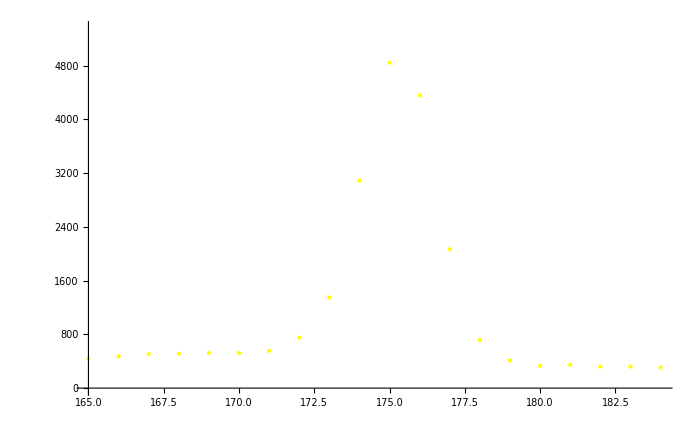

```mathematica
ListPlot[lst0,PlotRange->{Roi[175],All},PlotStyle->Directive@{PointSize[Large],Yellow},ImageSize->700,Axes->Full]
```